```mathematica
countryYearRanges={
{"Sweden",1808,1908}, 
{"EnglandWales-Civ",1808,1908},
{"France-Civ",1808,1908},
{"Denmark",1808,1908},
{"Netherlands",1808,1908}
};
```

```mathematica
countriesList=First@#&/@countryYearRanges(*,"Austria","Netherlands","HongKong","France-Civ","Denmark","Norway","USA"*);
Basedir="/Users/yifan/Library/CloudStorage/Dropbox/Current Projects/2023-AlonbLab-sickspans/Human healthspan/";
colNames=Association@{"Year"->1,"Age"->2,"Female"->3,"Male"->4,"Total"->5};
binYears=ToExpression[StringSplit[#,"-"]]&;
ggmParRanges={{.08,.13},{1.5,3.5},{6.,10.5},{3.5,7.}};
```

```mathematica
cMxTables=Import[FileNameJoin[{Basedir, "HMD",#,"cMx_1x5.txt"}],"Table","HeaderLines"->3]&/@countriesList;
cExposureTables=Import[FileNameJoin[{Basedir, "HMD",#,"cExposures_1x5.txt"}],"Table","HeaderLines"->3]&/@countriesList;
```

```mathematica
allhazards=
Table[(
cMxTable=cMxTables[[i]];
cExposureTable=cExposureTables[[i]];
years=Union@cMxTable[[;;,colNames[["Year"]]]];
ages = Union@cMxTable[[;;,colNames[["Age"]]]];
yearRange=Select[years,(binYears@#)[[1]]>countryYearRanges[[i,2]]&&(binYears@#)[[2]]<countryYearRanges[[i,3]]&&(#[[2]]-#[[1]]&@binYears@#==4)&];
hazards=Association@Table[gender->
	Association@Table[y->(
	(*Print[{countriesList[[i]],gender,cohort}];*)
	cMx=Select[cMxTable,First@#==y&&#[[2]]!="110+"&&#[[2]]!=0&][[;;,{"Age",gender}/.colNames]];
	cExposure=Select[cExposureTable,First@#==y&&#[[2]]!="110+"&&#[[2]]!=0&][[;;,{"Age",gender}/.colNames]];
	cDeaths=Select[Transpose@{cExposure[[;;,1]],Log@cMx[[;;,2]],cExposure[[;;,2]]*cMx[[;;,2]]},First@#>35.&];
	data=Select[cDeaths,#[[3]]>4.&&#[[1]]<105.&][[;;,{1,2}]]
),{y,yearRange}
],{gender,{"Female","Male"}}
]
),{i,Length@countriesList}];
```

```mathematica
allweights=
Table[(
cMxTable=cMxTables[[i]];
cExposureTable=cExposureTables[[i]];
years=Union@cMxTable[[;;,colNames[["Year"]]]];
ages = Union@cMxTable[[;;,colNames[["Age"]]]];
yearRange=Select[years,(binYears@#)[[1]]>countryYearRanges[[i,2]]&&(binYears@#)[[2]]<countryYearRanges[[i,3]]&&(#[[2]]-#[[1]]&@binYears@#==4)&];
hazards=Association@Table[gender->
	Association@Table[y->(
	(*Print[{countriesList[[i]],gender,cohort}];*)
	cMx=Select[cMxTable,First@#==y&&#[[2]]!="110+"&&#[[2]]!=0&][[;;,{"Age",gender}/.colNames]];
	cExposure=Select[cExposureTable,First@#==y&&#[[2]]!="110+"&&#[[2]]!=0&][[;;,{"Age",gender}/.colNames]];
	cDeaths=Select[Transpose@{cExposure[[;;,1]],Log@cMx[[;;,2]],cExposure[[;;,2]]*cMx[[;;,2]]},First@#>35.&];
	Sqrt@Select[cDeaths,#[[3]]>4.&&#[[1]]<105.&][[;;,3]]
),{y,yearRange}
],{gender,{"Female","Male"}}
]
),{i,Length@countriesList}];
```

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.111405 | 0.00258848 | 43.0387 | 5.79466×10^-49
s | 2.3065 | 0.169491 | 13.6084 | 1.47303×10^-20
a | 8.78057 | 0.210056 | 41.8011 | 3.51982×10^-48
m | 4.66656 | 0.0299978 | 155.563 | 2.99735×10^-84

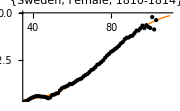

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.113117 | 0.00236819 | 47.7653 | 8.97539×10^-52
s | 2.39708 | 0.165694 | 14.4669 | 7.56509×10^-22
a | 8.96125 | 0.19265 | 46.5158 | 4.67239×10^-51
m | 4.72654 | 0.0277939 | 170.057 | 1.01545×10^-86

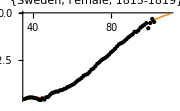

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.114686 | 0.00160737 | 71.3501 | 1.0155×10^-62
s | 2.35314 | 0.109207 | 21.5474 | 4.89903×10^-31
a | 9.13536 | 0.130893 | 69.7926 | 4.09705×10^-62
m | 4.79067 | 0.0189403 | 252.936 | 9.74064×10^-98

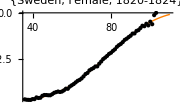

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.118661 | 0.00187817 | 63.1792 | 2.19007×10^-59
s | 2.16963 | 0.107482 | 20.1859 | 1.88359×10^-29
a | 9.47758 | 0.152513 | 62.1427 | 6.2084×10^-59
m | 4.82319 | 0.0211234 | 228.334 | 6.75556×10^-95

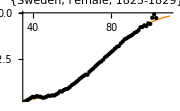

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.121116 | 0.00169517 | 71.4476 | 9.315×10^-63
s | 2.0767 | 0.0895764 | 23.1836 | 7.64709×10^-33
a | 9.71151 | 0.137635 | 70.5596 | 2.05345×10^-62
m | 4.863 | 0.0187242 | 259.718 | 1.79413×10^-98

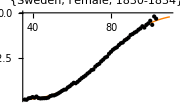

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.12451 | 0.00161905 | 76.9033 | 8.8538×10^-65
s | 2.0369 | 0.0815224 | 24.9857 | 1.01583×10^-34
a | 10.0135 | 0.131402 | 76.2048 | 1.57771×10^-64
m | 4.88928 | 0.0172827 | 282.901 | 7.57484×10^-101

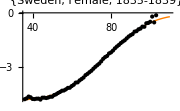

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.12478 | 0.0011766 | 106.051 | 1.21404×10^-73
s | 1.99717 | 0.0577274 | 34.5965 | 3.83608×10^-43
a | 10.0153 | 0.0951884 | 105.216 | 2.00848×10^-73
m | 4.9461 | 0.0130922 | 377.791 | 6.99323×10^-109

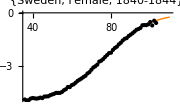

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.124896 | 0.00166343 | 75.0835 | 6.97789×10^-65
s | 2.03403 | 0.0826637 | 24.606 | 1.19643×10^-34
a | 10.0226 | 0.134772 | 74.3676 | 1.29147×10^-64
m | 4.9721 | 0.0191473 | 259.676 | 9.16274×10^-100

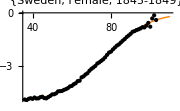

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.128477 | 0.00154824 | 82.9823 | 1.11895×10^-67
s | 1.78394 | 0.0618686 | 28.8344 | 9.39089×10^-39
a | 10.3012 | 0.124816 | 82.5312 | 1.58948×10^-67
m | 4.98525 | 0.016986 | 293.492 | 3.23054×10^-103

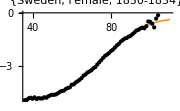

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.128449 | 0.00159096 | 80.7372 | 6.54264×10^-67
s | 1.7571 | 0.0622174 | 28.2413 | 3.286×10^-38
a | 10.2858 | 0.128042 | 80.3316 | 9.04757×10^-67
m | 5.02133 | 0.0179507 | 279.728 | 7.31253×10^-102

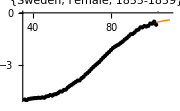

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.12508 | 0.00155885 | 80.2384 | 9.74949×10^-67
s | 1.77024 | 0.0634505 | 27.8995 | 6.83245×10^-38
a | 10.0123 | 0.125466 | 79.8005 | 1.38649×10^-66
m | 5.09355 | 0.0193382 | 263.393 | 3.6409×10^-100

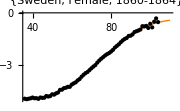

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.123598 | 0.00137819 | 89.6816 | 7.5137×10^-70
s | 1.75916 | 0.0563149 | 31.2379 | 7.28688×10^-41
a | 9.91503 | 0.111176 | 89.183 | 1.07647×10^-69
m | 5.12161 | 0.0176787 | 289.705 | 7.5087×10^-103

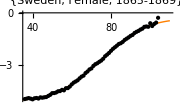

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.122626 | 0.00162944 | 75.2563 | 6.01907×10^-65
s | 1.72199 | 0.0654498 | 26.3101 | 2.27827×10^-36
a | 9.87317 | 0.13184 | 74.8872 | 8.25582×10^-65
m | 5.15071 | 0.0213771 | 240.946 | 1.18357×10^-97

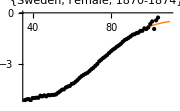

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.123397 | 0.00174133 | 70.8634 | 2.86578×10^-63
s | 1.64745 | 0.0668531 | 24.6428 | 1.09579×10^-34
a | 10.0007 | 0.141344 | 70.7539 | 3.16489×10^-63
m | 5.16232 | 0.022154 | 233.019 | 1.03846×10^-96

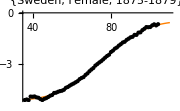

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.121379 | 0.00200994 | 60.3893 | 8.04342×10^-59
s | 1.66193 | 0.0806486 | 20.6071 | 3.32725×10^-30
a | 9.9087 | 0.163915 | 60.4504 | 7.54092×10^-59
m | 5.27272 | 0.0277283 | 190.157 | 5.57511×10^-91

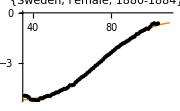

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.114032 | 0.0011173 | 102.06 | 1.7836×10^-73
s | 2.03607 | 0.0656874 | 30.9963 | 1.16985×10^-40
a | 9.40003 | 0.0921284 | 102.032 | 1.81598×10^-73
m | 5.50117 | 0.0200634 | 274.19 | 2.68026×10^-101

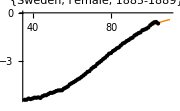

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.114115 | 0.000876642 | 130.173 | 2.60894×10^-80
s | 2.27654 | 0.0655583 | 34.7253 | 1.10024×10^-43
a | 9.53268 | 0.0729232 | 130.722 | 1.98609×10^-80
m | 5.61922 | 0.0165282 | 339.978 | 2.29797×10^-107

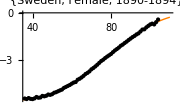

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.115037 | 0.00086716 | 132.659 | 7.66183×10^-81
s | 2.36643 | 0.07236 | 32.7036 | 4.41032×10^-42
a | 9.69629 | 0.072392 | 133.941 | 4.10893×10^-81
m | 5.77732 | 0.0175725 | 328.77 | 2.02841×10^-106

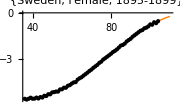

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.114837 | 0.000789693 | 145.419 | 1.99711×10^-83
s | 2.68093 | 0.0918681 | 29.1824 | 4.54966×10^-39
a | 9.7907 | 0.0663183 | 147.632 | 7.50547×10^-84
m | 5.99952 | 0.0182719 | 328.347 | 2.20544×10^-106

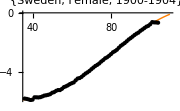

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.102109 | 0.00299471 | 34.0964 | 1.98696×10^-41
s | 3.26732 | 0.482954 | 6.76528 | 5.85677×10^-9
a | 7.90768 | 0.243305 | 32.5011 | 3.18007×10^-40
m | 4.40958 | 0.0340334 | 129.566 | 3.55441×10^-76

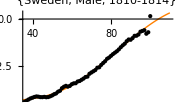

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.101608 | 0.00291534 | 34.8528 | 1.9482×10^-42
s | 3.60545 | 0.643979 | 5.59871 | 5.2439×10^-7
a | 7.89765 | 0.237864 | 33.2024 | 3.39206×10^-41
m | 4.55278 | 0.0378273 | 120.357 | 3.32875×10^-75

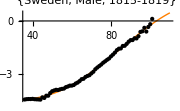

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.1044 | 0.00274772 | 37.995 | 3.81638×10^-45
s | 3.01014 | 0.346859 | 8.67828 | 2.33999×10^-12
a | 8.16166 | 0.223928 | 36.4478 | 4.68161×10^-44
m | 4.63491 | 0.035661 | 129.971 | 2.86564×10^-78

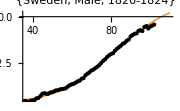

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110455 | 0.00220321 | 50.1339 | 1.72991×10^-52
s | 2.59743 | 0.185879 | 13.9738 | 5.73068×10^-21
a | 8.68835 | 0.178973 | 48.5455 | 1.25035×10^-51
m | 4.6173 | 0.0250814 | 184.093 | 9.06731×10^-88

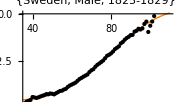

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.112979 | 0.00172987 | 65.3106 | 1.37501×10^-59
s | 2.52179 | 0.135707 | 18.5825 | 2.94262×10^-27
a | 8.92647 | 0.140503 | 63.5321 | 7.63128×10^-59
m | 4.66568 | 0.0194861 | 239.436 | 5.97118×10^-95

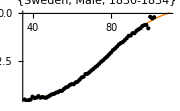

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.112065 | 0.00167443 | 66.9275 | 5.78174×10^-61
s | 2.46377 | 0.125008 | 19.7089 | 7.0622×10^-29
a | 8.84845 | 0.135992 | 65.0659 | 3.42708×10^-60
m | 4.76207 | 0.0207661 | 229.319 | 5.12967×10^-95

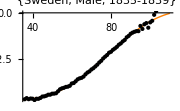

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.107052 | 0.0013831 | 77.4 | 2.13673×10^-63
s | 3.22021 | 0.220287 | 14.6183 | 9.29483×10^-22
a | 8.45245 | 0.112472 | 75.1515 | 1.30404×10^-62
m | 4.90506 | 0.0205645 | 238.521 | 1.40293×10^-93

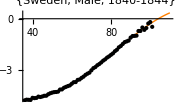

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.108192 | 0.00174713 | 61.9259 | 7.73681×10^-59
s | 2.96623 | 0.211991 | 13.9923 | 3.86031×10^-21
a | 8.53924 | 0.14226 | 60.0257 | 5.49979×10^-58
m | 4.96641 | 0.0274693 | 180.799 | 2.03055×10^-88

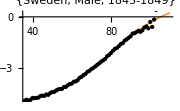

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110929 | 0.00197439 | 56.1837 | 1.54215×10^-55
s | 2.67199 | 0.182884 | 14.6103 | 6.64586×10^-22
a | 8.77632 | 0.160333 | 54.7382 | 7.71275×10^-55
m | 4.94643 | 0.0287497 | 172.052 | 6.37741×10^-86

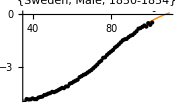

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.113307 | 0.00176302 | 64.2684 | 7.45828×10^-60
s | 2.4561 | 0.13216 | 18.5843 | 1.74837×10^-27
a | 8.96378 | 0.142816 | 62.7648 | 3.31533×10^-59
m | 4.9801 | 0.0254847 | 195.416 | 1.41452×10^-90

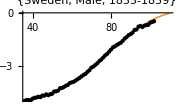

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.115099 | 0.00135249 | 85.1015 | 1.4405×10^-67
s | 2.2247 | 0.0831942 | 26.7411 | 1.91528×10^-36
a | 9.11112 | 0.109138 | 83.4829 | 4.87039×10^-67
m | 5.01457 | 0.0192011 | 261.16 | 1.25892×10^-98

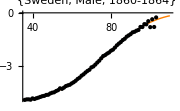

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.114815 | 0.00140488 | 81.7262 | 2.98794×10^-67
s | 2.20186 | 0.0853359 | 25.8023 | 7.25196×10^-36
a | 9.09529 | 0.113323 | 80.2601 | 9.58092×10^-67
m | 5.10145 | 0.0214019 | 238.364 | 2.38178×10^-97

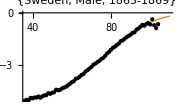

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.11439 | 0.0013958 | 81.9534 | 2.49889×10^-67
s | 2.17131 | 0.0832384 | 26.0855 | 3.79364×10^-36
a | 9.08996 | 0.11282 | 80.5705 | 7.47329×10^-67
m | 5.16977 | 0.0223798 | 231.002 | 1.82615×10^-96

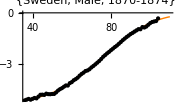

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.114593 | 0.00190578 | 60.1289 | 1.06007×10^-58
s | 2.13306 | 0.110334 | 19.3328 | 1.18825×10^-28
a | 9.14043 | 0.154369 | 59.2115 | 2.82934×10^-58
m | 5.20578 | 0.0309246 | 168.338 | 1.51304×10^-87

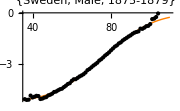

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.115179 | 0.00212708 | 54.1487 | 8.42201×10^-56
s | 2.0748 | 0.118622 | 17.4908 | 2.83138×10^-26
a | 9.19778 | 0.171949 | 53.4913 | 1.83136×10^-55
m | 5.27601 | 0.0356699 | 147.912 | 6.63801×10^-84

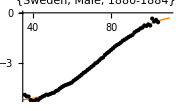

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110446 | 0.000991221 | 111.424 | 6.1265×10^-76
s | 2.19692 | 0.0638847 | 34.3888 | 2.00639×10^-43
a | 8.80274 | 0.0801194 | 109.87 | 1.51922×10^-75
m | 5.54498 | 0.0223548 | 248.045 | 1.79629×10^-98

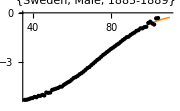

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.11337 | 0.00104372 | 108.621 | 3.18149×10^-75
s | 2.01236 | 0.0573547 | 35.0862 | 5.81066×10^-44
a | 9.03809 | 0.0838709 | 107.762 | 5.31633×10^-75
m | 5.63184 | 0.0236245 | 238.389 | 2.36563×10^-97

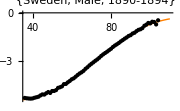

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.111052 | 0.00146602 | 75.7507 | 3.95135×10^-65
s | 2.14525 | 0.0921849 | 23.2712 | 3.12045×10^-33
a | 8.85314 | 0.117769 | 75.1739 | 6.45818×10^-65
m | 5.86181 | 0.0414502 | 141.418 | 1.21785×10^-82

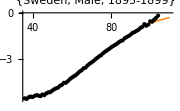

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.107794 | 0.0015737 | 68.4967 | 2.53311×10^-62
s | 2.23137 | 0.111787 | 19.9609 | 1.99787×10^-29
a | 8.59079 | 0.126082 | 68.1366 | 3.55184×10^-62
m | 6.26085 | 0.0650525 | 96.2429 | 7.89403×10^-72

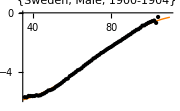

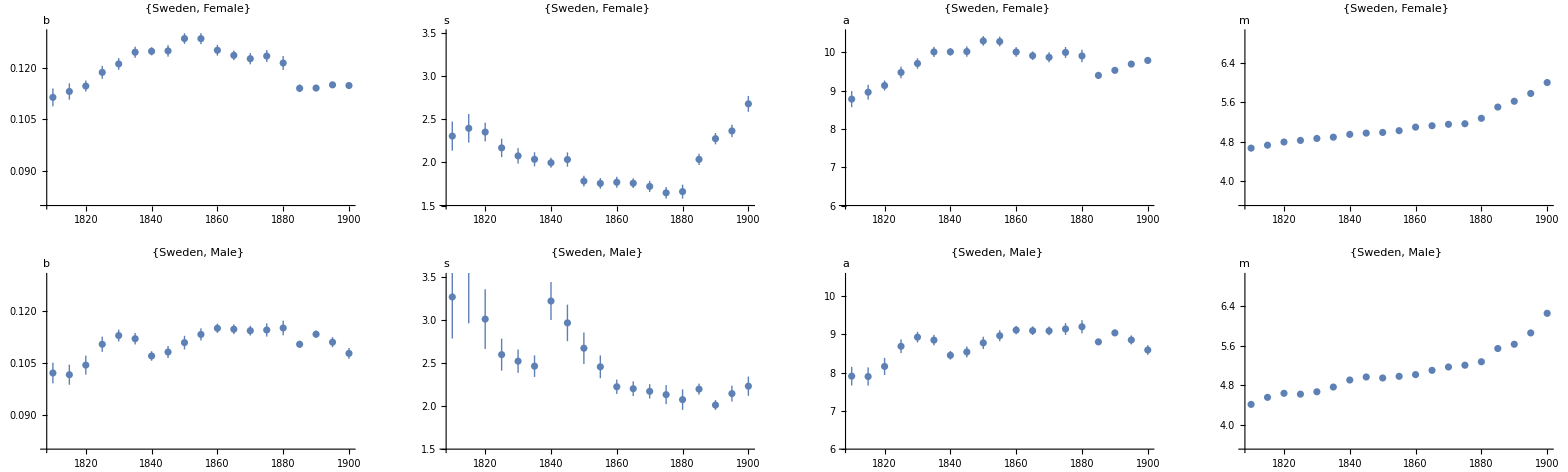

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.107943 | 0.00233222 | 46.2833 | 1.75905×10^-51
s | 1.7954 | 0.0948355 | 18.9317 | 3.79168×10^-28
a | 8.17267 | 0.184788 | 44.2273 | 3.08373×10^-50
m | 4.59666 | 0.029675 | 154.9 | 3.33049×10^-85

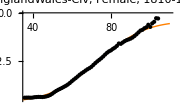

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.105469 | 0.00184306 | 57.2252 | 2.49483×10^-57
s | 1.90049 | 0.0844042 | 22.5166 | 2.1066×10^-32
a | 8.01553 | 0.146565 | 54.6893 | 4.47614×10^-56
m | 4.66316 | 0.0253305 | 184.093 | 4.56559×10^-90

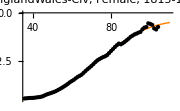

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0980979 | 0.0019114 | 51.3224 | 2.53846×10^-54
s | 2.15258 | 0.11052 | 19.4768 | 7.86643×10^-29
a | 7.39097 | 0.153006 | 48.3052 | 1.18004×10^-52
m | 4.73684 | 0.0326377 | 145.134 | 2.26781×10^-83

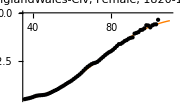

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0995045 | 0.00188293 | 52.8455 | 3.9634×10^-55
s | 2.16946 | 0.11114 | 19.5201 | 6.95141×10^-29
a | 7.55693 | 0.151105 | 50.0111 | 1.31052×10^-53
m | 4.69508 | 0.0295346 | 158.969 | 6.20184×10^-86

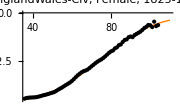

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.094597 | 0.00178929 | 52.8685 | 3.85548×10^-55
s | 2.4714 | 0.140357 | 17.6079 | 1.97684×10^-26
a | 7.17567 | 0.144792 | 49.5584 | 2.33167×10^-53
m | 4.75433 | 0.0324454 | 146.533 | 1.21806×10^-83

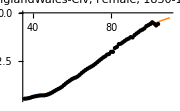

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0969675 | 0.00156465 | 61.9738 | 1.53686×10^-59
s | 2.5676 | 0.133145 | 19.2842 | 1.36653×10^-28
a | 7.43611 | 0.127064 | 58.5225 | 5.97185×10^-58
m | 4.75206 | 0.0264849 | 179.425 | 2.41551×10^-89

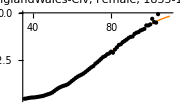

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0987656 | 0.00176208 | 56.0507 | 9.35412×10^-57
s | 2.56833 | 0.149918 | 17.1316 | 8.60967×10^-26
a | 7.61997 | 0.143294 | 53.1772 | 2.663×10^-55
m | 4.76351 | 0.0288146 | 165.316 | 4.89759×10^-87

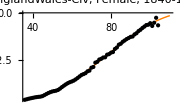

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.102715 | 0.00167786 | 61.2175 | 3.3691×10^-59
s | 2.36863 | 0.118848 | 19.9299 | 2.17955×10^-29
a | 7.99796 | 0.136544 | 58.5742 | 5.64479×10^-58
m | 4.71708 | 0.0240365 | 196.247 | 7.20947×10^-92

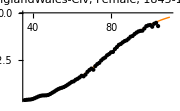

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.108838 | 0.00190652 | 57.0871 | 2.91017×10^-57
s | 2.08928 | 0.103645 | 20.158 | 1.15133×10^-29
a | 8.53543 | 0.154552 | 55.2268 | 2.40179×10^-56
m | 4.75569 | 0.02489 | 191.068 | 4.08798×10^-91

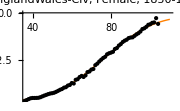

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.108088 | 0.00158837 | 68.0498 | 3.85414×10^-62
s | 2.08824 | 0.0878866 | 23.7606 | 9.28003×10^-34
a | 8.51801 | 0.129155 | 65.9521 | 2.86687×10^-61
m | 4.83538 | 0.0219548 | 220.243 | 4.0386×10^-95

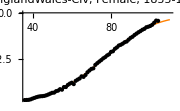

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.10927 | 0.00189813 | 57.5669 | 1.70676×10^-57
s | 2.0081 | 0.100226 | 20.0358 | 1.61959×10^-29
a | 8.64312 | 0.15389 | 56.1641 | 8.22411×10^-57
m | 4.99825 | 0.0286074 | 174.719 | 1.35476×10^-88

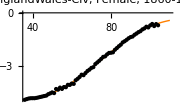

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.107642 | 0.00153881 | 69.9518 | 6.57768×10^-63
s | 2.15022 | 0.0940088 | 22.8725 | 8.50587×10^-33
a | 8.57517 | 0.125513 | 68.3212 | 2.98605×10^-62
m | 5.10398 | 0.0255586 | 199.698 | 2.32606×10^-92

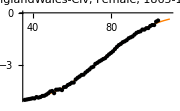

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.107667 | 0.00143621 | 74.9659 | 7.7174×10^-65
s | 2.08391 | 0.0848693 | 24.5543 | 1.35387×10^-34
a | 8.60566 | 0.116995 | 73.556 | 2.61375×10^-64
m | 5.28308 | 0.0269106 | 196.32 | 7.03732×10^-92

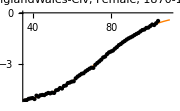

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.107987 | 0.0015321 | 70.4827 | 4.04948×10^-63
s | 2.15133 | 0.0976454 | 22.0321 | 7.3716×10^-32
a | 8.71015 | 0.125488 | 69.4102 | 1.08301×10^-62
m | 5.34065 | 0.0290881 | 183.603 | 5.42685×10^-90

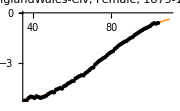

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110767 | 0.00149063 | 74.3087 | 1.35894×10^-64
s | 2.03624 | 0.0870359 | 23.3955 | 2.28909×10^-33
a | 9.00976 | 0.122201 | 73.7287 | 2.24828×10^-64
m | 5.42644 | 0.0279094 | 194.431 | 1.31797×10^-91

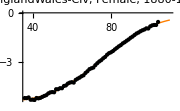

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110288 | 0.00119726 | 92.1174 | 1.33414×10^-70
s | 2.08758 | 0.0749382 | 27.8574 | 7.48134×10^-38
a | 9.03412 | 0.0985134 | 91.7045 | 1.78258×10^-70
m | 5.56178 | 0.0245677 | 226.386 | 6.77183×10^-96

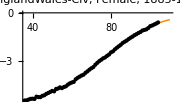

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.11217 | 0.0010686 | 104.97 | 2.90141×10^-74
s | 2.00208 | 0.0627586 | 31.9013 | 2.01891×10^-41
a | 9.24111 | 0.0879195 | 105.109 | 2.66317×10^-74
m | 5.66949 | 0.0223807 | 253.321 | 4.57977×10^-99

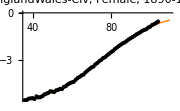

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.109831 | 0.000946305 | 116.063 | 4.3797×10^-77
s | 2.19734 | 0.068543 | 32.0578 | 1.49657×10^-41
a | 9.11471 | 0.0782212 | 116.525 | 3.38764×10^-77
m | 5.84134 | 0.0229207 | 254.85 | 3.09834×10^-99

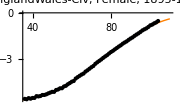

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.105787 | 0.000914502 | 115.677 | 5.43379×10^-77
s | 2.56257 | 0.0979338 | 26.1663 | 3.15652×10^-36
a | 8.84558 | 0.0759764 | 116.425 | 3.58027×10^-77
m | 6.10824 | 0.0286333 | 213.326 | 3.20455×10^-94

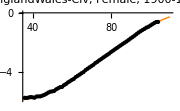

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0948202 | 0.00178479 | 53.1267 | 1.16944×10^-54
s | 2.31829 | 0.115309 | 20.1051 | 2.35285×10^-29
a | 6.92588 | 0.141103 | 49.0838 | 1.64441×10^-52
m | 4.72553 | 0.0355243 | 133.022 | 6.52115×10^-80

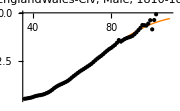

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0912306 | 0.00185974 | 49.0555 | 1.70477×10^-52
s | 2.62407 | 0.162091 | 16.1888 | 2.597×10^-24
a | 6.67697 | 0.148073 | 45.0925 | 3.22167×10^-50
m | 4.79621 | 0.0416847 | 115.059 | 6.75917×10^-76

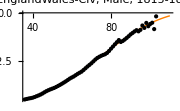

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0865447 | 0.00185656 | 46.6157 | 4.08869×10^-51
s | 2.86705 | 0.202896 | 14.1307 | 2.39284×10^-21
a | 6.26767 | 0.148639 | 42.1671 | 2.05397×10^-48
m | 4.82184 | 0.0479507 | 100.558 | 3.57942×10^-72

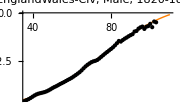

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0898512 | 0.00181808 | 49.421 | 1.07291×10^-52
s | 2.98356 | 0.219882 | 13.5689 | 1.6925×10^-20
a | 6.61102 | 0.146013 | 45.2771 | 2.50003×10^-50
m | 4.64183 | 0.0360961 | 128.596 | 5.64202×10^-79

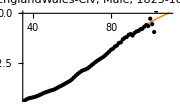

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0910022 | 0.00193721 | 46.9759 | 6.88633×10^-52
s | 2.69559 | 0.178012 | 15.1428 | 5.3705×10^-23
a | 6.67835 | 0.155146 | 43.0456 | 1.6934×10^-49
m | 4.60328 | 0.0367716 | 125.186 | 3.27244×10^-79

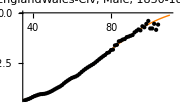

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0937521 | 0.00158312 | 59.22 | 5.94902×10^-57
s | 2.68004 | 0.14461 | 18.5328 | 3.39515×10^-27
a | 6.93308 | 0.126383 | 54.8577 | 6.74126×10^-55
m | 4.60559 | 0.0278284 | 165.5 | 7.32135×10^-85

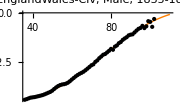

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0937587 | 0.00226739 | 41.351 | 2.10453×10^-48
s | 2.79373 | 0.22683 | 12.3164 | 1.18368×10^-18
a | 6.9554 | 0.18176 | 38.2669 | 2.66761×10^-46
m | 4.65485 | 0.041925 | 111.028 | 7.71338×10^-76

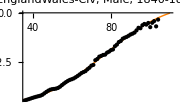

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0929611 | 0.00193177 | 48.1222 | 1.50026×10^-52
s | 2.95373 | 0.225254 | 13.1129 | 6.37585×10^-20
a | 6.91707 | 0.155425 | 44.5043 | 2.08175×10^-50
m | 4.67306 | 0.0366122 | 127.637 | 9.32591×10^-80

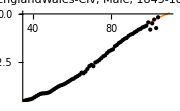

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0997669 | 0.002212 | 45.1025 | 8.9765×10^-51
s | 2.52543 | 0.17115 | 14.7557 | 1.98954×10^-22
a | 7.49833 | 0.176863 | 42.3963 | 4.39768×10^-49
m | 4.67632 | 0.0362966 | 128.836 | 5.08937×10^-80

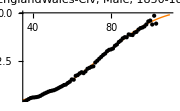

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.100798 | 0.00200244 | 50.3376 | 8.67638×10^-54
s | 2.48636 | 0.150246 | 16.5486 | 5.40391×10^-25
a | 7.60442 | 0.160118 | 47.4926 | 3.44999×10^-52
m | 4.74149 | 0.0336924 | 140.729 | 1.67135×10^-82

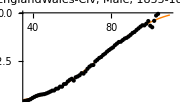

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.104607 | 0.00216092 | 48.4086 | 1.03069×10^-52
s | 2.27049 | 0.134972 | 16.822 | 2.2724×10^-25
a | 7.93786 | 0.171827 | 46.1968 | 1.97947×10^-51
m | 4.85801 | 0.0364946 | 133.116 | 6.13217×10^-81

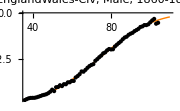

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.103171 | 0.00192811 | 53.509 | 1.79318×10^-55
s | 2.3831 | 0.13525 | 17.62 | 1.90538×10^-26
a | 7.87065 | 0.15409 | 51.0784 | 3.43502×10^-54
m | 4.97199 | 0.0363396 | 136.82 | 1.03652×10^-81

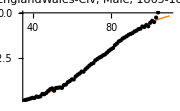

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.104481 | 0.00230544 | 45.3192 | 6.63665×10^-51
s | 2.23452 | 0.143826 | 15.5363 | 1.44629×10^-23
a | 7.99015 | 0.183658 | 43.5057 | 8.68019×10^-50
m | 5.09413 | 0.0461923 | 110.281 | 1.19361×10^-75

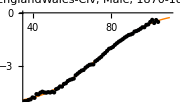

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.108084 | 0.00263762 | 40.9779 | 3.71309×10^-48
s | 1.98168 | 0.130527 | 15.1822 | 4.70553×10^-23
a | 8.28071 | 0.209365 | 39.5514 | 3.40323×10^-47
m | 5.03018 | 0.0469292 | 107.187 | 7.51531×10^-75

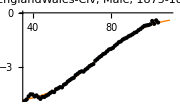

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.104959 | 0.00235203 | 44.6251 | 1.75495×10^-50
s | 1.96609 | 0.11862 | 16.5748 | 4.97177×10^-25
a | 8.00259 | 0.186014 | 43.0214 | 1.7542×10^-49
m | 5.26141 | 0.0535722 | 98.2115 | 2.13578×10^-72

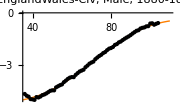

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0969582 | 0.00119192 | 81.346 | 4.03394×10^-67
s | 2.22374 | 0.0787568 | 28.2355 | 3.32662×10^-38
a | 7.33067 | 0.0944845 | 77.586 | 8.47731×10^-66
m | 5.75853 | 0.0495071 | 116.317 | 3.80172×10^-77

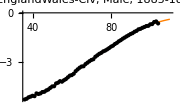

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0982801 | 0.0013475 | 72.9352 | 4.50521×10^-64
s | 2.12095 | 0.0819637 | 25.8767 | 6.11361×10^-36
a | 7.43955 | 0.106309 | 69.9802 | 6.4086×10^-63
m | 5.9866 | 0.0657941 | 90.9899 | 2.95263×10^-70

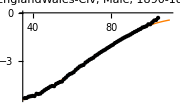

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0976573 | 0.00173118 | 56.4107 | 6.22061×10^-57
s | 2.05198 | 0.100768 | 20.3635 | 6.50834×10^-30
a | 7.37466 | 0.136042 | 54.2088 | 7.84814×10^-56
m | 6.26324 | 0.109745 | 57.0709 | 2.96346×10^-57

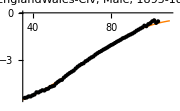

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.096623 | 0.00242283 | 39.8802 | 2.02909×10^-47
s | 2.0679 | 0.146354 | 14.1295 | 1.72245×10^-21
a | 7.32559 | 0.19063 | 38.4282 | 2.05256×10^-46
m | 6.54363 | 0.198641 | 32.9419 | 2.82476×10^-42

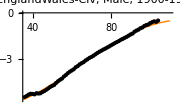

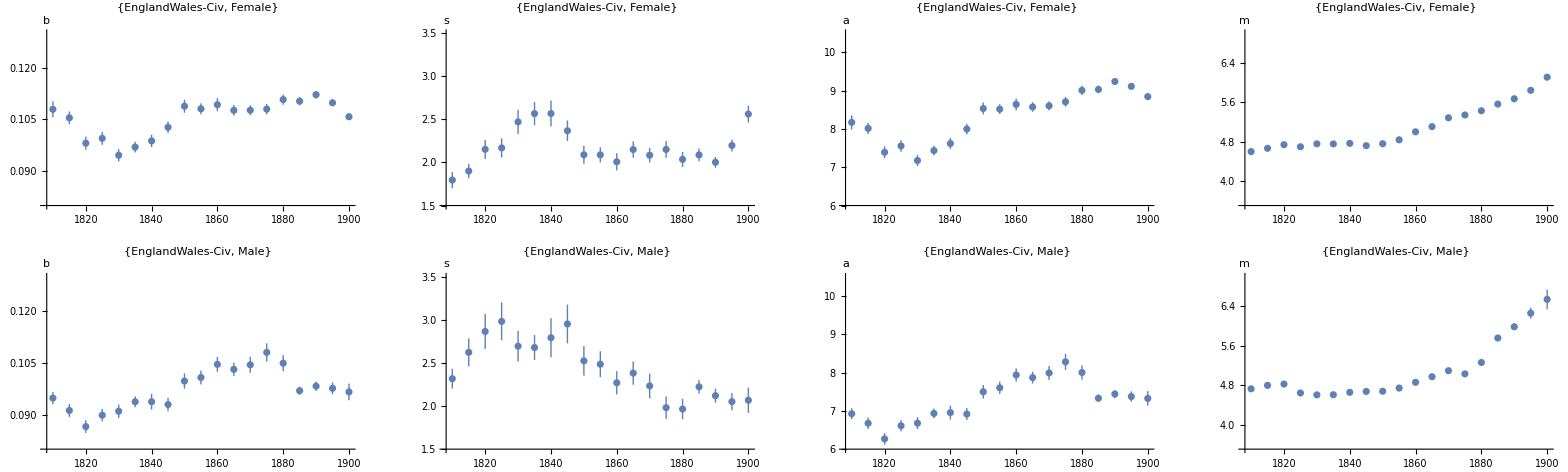

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.113555 | 0.00200411 | 56.6609 | 4.69242×10^-57
s | 2.04476 | 0.0979779 | 20.8696 | 1.62561×10^-30
a | 8.6769 | 0.158881 | 54.6124 | 4.89546×10^-56
m | 4.60234 | 0.0235184 | 195.691 | 8.66606×10^-92

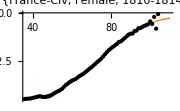

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.11552 | 0.00272526 | 42.3886 | 4.44868×10^-49
s | 1.97212 | 0.123981 | 15.9066 | 4.28335×10^-24
a | 8.79982 | 0.21489 | 40.9503 | 3.8727×10^-48
m | 4.66116 | 0.0327096 | 142.501 | 7.42803×10^-83

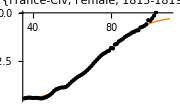

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.11161 | 0.00233021 | 47.8968 | 2.01878×10^-52
s | 2.10741 | 0.121515 | 17.3428 | 4.46952×10^-26
a | 8.49681 | 0.184367 | 46.0865 | 2.30181×10^-51
m | 4.74161 | 0.0317037 | 149.56 | 3.23654×10^-84

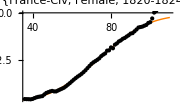

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.112239 | 0.00259957 | 43.1759 | 1.40046×10^-49
s | 2.13136 | 0.137381 | 15.5143 | 1.55545×10^-23
a | 8.57458 | 0.206186 | 41.5866 | 1.47413×10^-48
m | 4.70189 | 0.033671 | 139.642 | 2.76161×10^-82

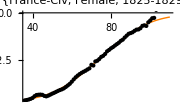

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.118715 | 0.00256416 | 46.298 | 1.72433×10^-51
s | 1.91449 | 0.109356 | 17.5069 | 2.6948×10^-26
a | 9.12253 | 0.202777 | 44.9881 | 1.05352×10^-50
m | 4.63841 | 0.0281064 | 165.031 | 5.47843×10^-87

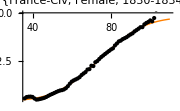

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.115925 | 0.00165833 | 69.9043 | 3.70308×10^-62
s | 1.98538 | 0.0776017 | 25.5843 | 2.55742×10^-35
a | 8.9193 | 0.131251 | 67.9559 | 2.20801×10^-61
m | 4.77006 | 0.0207589 | 229.784 | 4.5065×10^-95

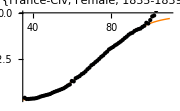

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.114461 | 0.00179493 | 63.7689 | 2.4741×10^-60
s | 1.99414 | 0.0862594 | 23.118 | 4.5802×10^-33
a | 8.82306 | 0.142419 | 61.9515 | 1.57264×10^-59
m | 4.80776 | 0.0235012 | 204.575 | 4.85847×10^-93

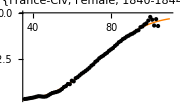

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.115511 | 0.00184048 | 62.7615 | 6.8525×10^-60
s | 2.06413 | 0.093675 | 22.035 | 7.31531×10^-32
a | 8.97221 | 0.146963 | 61.0507 | 4.01074×10^-59
m | 4.76991 | 0.0227086 | 210.048 | 8.75518×10^-94

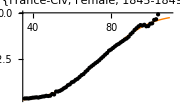

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.112374 | 0.00173911 | 64.6157 | 1.06344×10^-60
s | 2.19091 | 0.101076 | 21.6758 | 1.87698×10^-31
a | 8.75946 | 0.139655 | 62.722 | 7.13412×10^-60
m | 4.87825 | 0.0243649 | 200.216 | 1.96571×10^-92

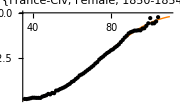

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.116863 | 0.00196523 | 59.4654 | 2.15305×10^-58
s | 1.90671 | 0.0880331 | 21.659 | 1.96215×10^-31
a | 9.13402 | 0.157272 | 58.0779 | 9.71442×10^-58
m | 4.87151 | 0.0252087 | 193.247 | 1.9587×10^-91

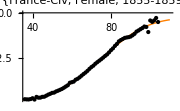

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.118249 | 0.00205486 | 57.546 | 1.74678×10^-57
s | 1.73525 | 0.0803336 | 21.6006 | 2.28973×10^-31
a | 9.27457 | 0.164388 | 56.4189 | 6.16381×10^-57
m | 4.87175 | 0.0253203 | 192.405 | 2.60077×10^-91

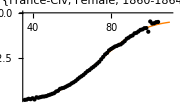

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110796 | 0.00152967 | 72.4314 | 7.03156×10^-64
s | 1.95278 | 0.0759991 | 25.6947 | 9.29008×10^-36
a | 8.73234 | 0.123452 | 70.7346 | 3.22088×10^-63
m | 5.00569 | 0.0230349 | 217.309 | 9.64588×10^-95

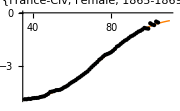

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.106742 | 0.0014517 | 73.5288 | 2.67677×10^-64
s | 2.16257 | 0.0899391 | 24.0449 | 4.63062×10^-34
a | 8.50678 | 0.118643 | 71.7009 | 1.34806×10^-63
m | 5.04471 | 0.0234673 | 214.968 | 1.94858×10^-94

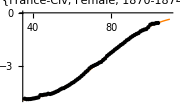

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.106693 | 0.00153155 | 69.6634 | 8.57432×10^-63
s | 2.29746 | 0.109062 | 21.0656 | 9.56164×10^-31
a | 8.61522 | 0.126434 | 68.1402 | 3.53977×10^-62
m | 5.0483 | 0.0240009 | 210.338 | 8.00613×10^-94

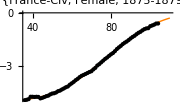

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110768 | 0.00187224 | 59.1637 | 2.97911×10^-58
s | 2.24431 | 0.127862 | 17.5526 | 2.34198×10^-26
a | 9.08666 | 0.15567 | 58.3714 | 7.04288×10^-58
m | 5.04871 | 0.0260057 | 194.139 | 1.45299×10^-91

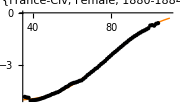

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.113722 | 0.00180372 | 63.0488 | 5.11685×10^-60
s | 2.15422 | 0.115311 | 18.6819 | 7.87871×10^-28
a | 9.43317 | 0.150567 | 62.6508 | 7.67177×10^-60
m | 5.13104 | 0.0244347 | 209.99 | 8.91466×10^-94

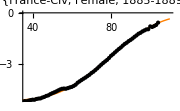

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.11939 | 0.00155023 | 77.0143 | 1.36404×10^-65
s | 1.91953 | 0.0804838 | 23.8499 | 7.45467×10^-34
a | 10.0005 | 0.129549 | 77.1949 | 1.1733×10^-65
m | 5.19428 | 0.0194262 | 267.386 | 1.37054×10^-100

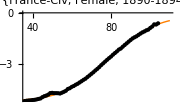

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.118454 | 0.000998393 | 118.645 | 1.05498×10^-77
s | 1.98961 | 0.057308 | 34.7178 | 1.11513×10^-43
a | 10.0127 | 0.0837856 | 119.503 | 6.61721×10^-78
m | 5.35212 | 0.013767 | 388.765 | 3.78304×10^-111

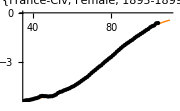

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.115546 | 0.00113115 | 102.149 | 1.68577×10^-73
s | 2.28044 | 0.0897364 | 25.4127 | 1.78563×10^-35
a | 9.89496 | 0.0957239 | 103.37 | 7.82675×10^-74
m | 5.53029 | 0.0178261 | 310.236 | 8.79271×10^-105

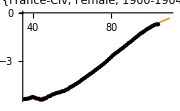

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.104684 | 0.00196327 | 53.3213 | 3.8888×10^-54
s | 2.57023 | 0.15511 | 16.5704 | 1.20037×10^-24
a | 7.80321 | 0.154479 | 50.5132 | 1.08827×10^-52
m | 4.71056 | 0.0313185 | 150.408 | 2.9802×10^-82

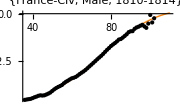

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.104777 | 0.00307065 | 34.122 | 3.24256×10^-43
s | 2.59648 | 0.244836 | 10.605 | 8.17748×10^-16
a | 7.79189 | 0.241595 | 32.2519 | 1.03415×10^-41
m | 4.75601 | 0.0518285 | 91.7644 | 1.7091×10^-70

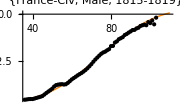

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.102441 | 0.00320171 | 31.9957 | 4.35612×10^-41
s | 2.72495 | 0.291019 | 9.3635 | 1.31821×10^-13
a | 7.6089 | 0.25245 | 30.1402 | 1.57671×10^-39
m | 4.79873 | 0.0582331 | 82.4055 | 1.10999×10^-66

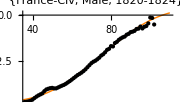

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.107501 | 0.0031631 | 33.9861 | 1.13119×10^-42
s | 2.38576 | 0.207372 | 11.5047 | 3.16079×10^-17
a | 8.01806 | 0.248342 | 32.2864 | 2.52403×10^-41
m | 4.65983 | 0.0461602 | 100.949 | 2.79665×10^-72

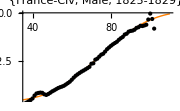

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.117452 | 0.00213032 | 55.1336 | 4.94582×10^-55
s | 1.98126 | 0.0955141 | 20.7432 | 7.51705×10^-30
a | 8.82811 | 0.165793 | 53.2479 | 4.23374×10^-54
m | 4.54505 | 0.0233436 | 194.702 | 2.67373×10^-89

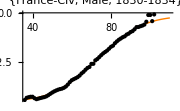

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.109916 | 0.00156787 | 70.1056 | 1.68184×10^-61
s | 2.22084 | 0.0891169 | 24.9206 | 2.48378×10^-34
a | 8.20295 | 0.122275 | 67.0859 | 2.59876×10^-60
m | 4.73082 | 0.0229063 | 206.53 | 6.54646×10^-91

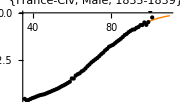

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.104217 | 0.00151984 | 68.5712 | 6.66157×10^-61
s | 2.34937 | 0.0996202 | 23.5833 | 5.75819×10^-33
a | 7.74568 | 0.119122 | 65.0232 | 1.80809×10^-59
m | 4.77582 | 0.0255326 | 187.048 | 3.33076×10^-88

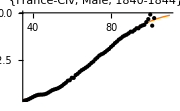

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.101955 | 0.0014739 | 69.1736 | 3.86683×10^-61
s | 2.49765 | 0.111101 | 22.4808 | 8.57373×10^-32
a | 7.5909 | 0.116279 | 65.282 | 1.41293×10^-59
m | 4.73727 | 0.0248973 | 190.272 | 1.13685×10^-88

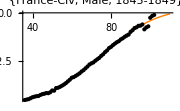

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.102715 | 0.00217322 | 47.2641 | 4.67908×10^-52
s | 2.47645 | 0.159365 | 15.5396 | 1.43074×10^-23
a | 7.68292 | 0.172209 | 44.614 | 1.78277×10^-50
m | 4.72247 | 0.0359098 | 131.509 | 1.34646×10^-80

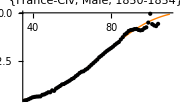

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.104892 | 0.00217181 | 48.2972 | 1.19236×10^-52
s | 2.32404 | 0.136586 | 17.0152 | 1.23847×10^-25
a | 7.85768 | 0.171894 | 45.7124 | 3.84903×10^-51
m | 4.7037 | 0.033967 | 138.478 | 4.74923×10^-82

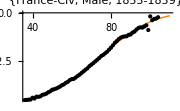

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.10654 | 0.00242377 | 43.9562 | 4.54061×10^-50
s | 2.06858 | 0.122278 | 16.9171 | 1.68455×10^-25
a | 7.98319 | 0.191136 | 41.7671 | 1.12353×10^-48
m | 4.70625 | 0.0365942 | 128.607 | 5.71306×10^-80

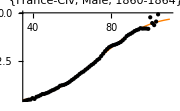

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.100303 | 0.002776 | 36.1321 | 9.43737×10^-45
s | 2.21463 | 0.164972 | 13.4242 | 2.07996×10^-20
a | 7.50702 | 0.220548 | 34.0381 | 3.77398×10^-43
m | 4.77541 | 0.0492171 | 97.0276 | 4.67352×10^-72

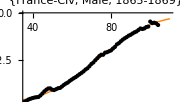

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0998463 | 0.00574064 | 17.3929 | 3.82869×10^-26
s | 2.25688 | 0.357124 | 6.31961 | 2.71042×10^-8
a | 7.5716 | 0.461782 | 16.3965 | 8.78585×10^-25
m | 4.63134 | 0.089462 | 51.7688 | 1.46521×10^-54

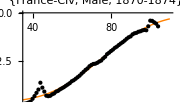

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.104015 | 0.00590255 | 17.6221 | 1.89328×10^-26
s | 2.15108 | 0.3319 | 6.4811 | 1.41721×10^-8
a | 8.01325 | 0.478193 | 16.7574 | 2.78642×10^-25
m | 4.50819 | 0.0759553 | 59.3532 | 2.42908×10^-58

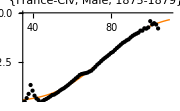

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0916649 | 0.00312749 | 29.3094 | 3.49852×10^-39
s | 2.93034 | 0.383455 | 7.64193 | 1.2629×10^-10
a | 7.03675 | 0.256634 | 27.4194 | 1.93546×10^-37
m | 4.87721 | 0.0660896 | 73.797 | 2.11849×10^-64

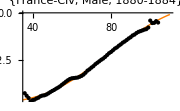

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0897311 | 0.00253538 | 35.3915 | 3.40112×10^-44
s | 3.2562 | 0.434016 | 7.5025 | 2.23352×10^-10
a | 6.92036 | 0.20892 | 33.1244 | 2.01209×10^-42
m | 5.0375 | 0.0619346 | 81.3358 | 4.06653×10^-67

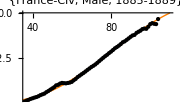

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0957333 | 0.0024078 | 39.7597 | 2.45153×10^-47
s | 2.62976 | 0.228842 | 11.4916 | 2.64902×10^-17
a | 7.46651 | 0.197444 | 37.8158 | 5.58091×10^-46
m | 4.97866 | 0.0477181 | 104.335 | 4.29312×10^-74

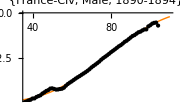

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0967108 | 0.00212185 | 45.5785 | 4.63159×10^-51
s | 2.47298 | 0.17619 | 14.0359 | 2.389×10^-21
a | 7.55659 | 0.173519 | 43.549 | 8.15364×10^-50
m | 5.04546 | 0.0430625 | 117.166 | 2.37527×10^-77

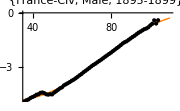

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0919261 | 0.00249488 | 36.8458 | 2.80542×10^-45
s | 2.7404 | 0.279466 | 9.80585 | 1.93174×10^-14
a | 7.19626 | 0.204839 | 35.1313 | 5.36679×10^-44
m | 5.32646 | 0.0693937 | 76.7571 | 1.69129×10^-65

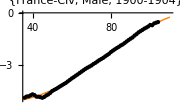

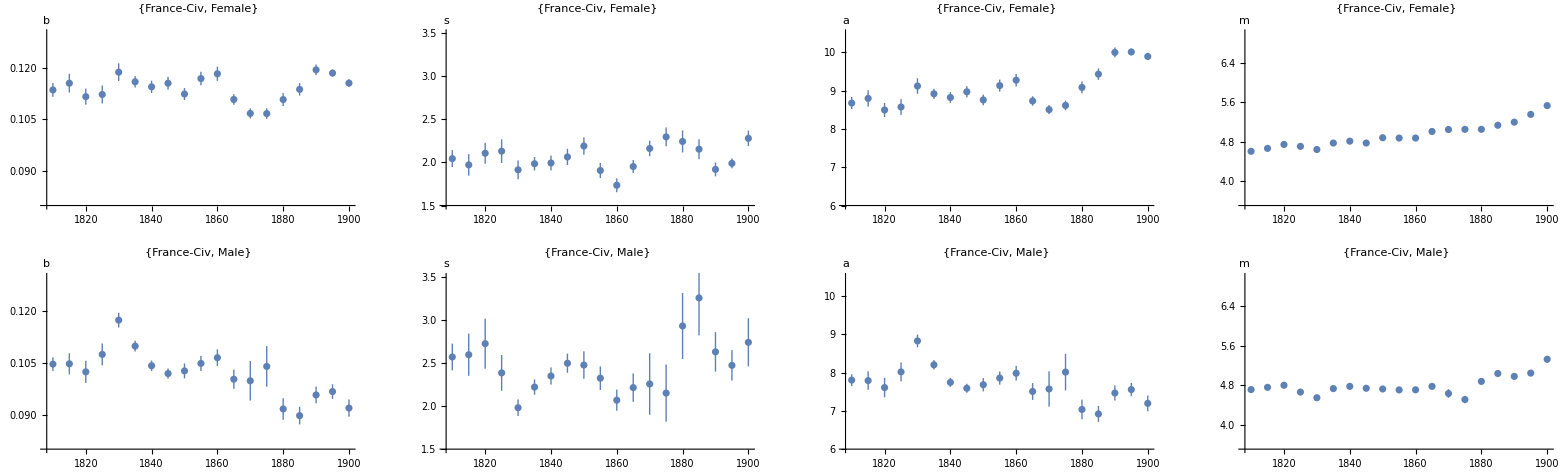

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110513 | 0.00209088 | 52.8549 | 2.79205×10^-53
s | 2.43493 | 0.154958 | 15.7135 | 2.69236×10^-23
a | 8.66005 | 0.168699 | 51.3342 | 1.63948×10^-52
m | 4.7277 | 0.0259613 | 182.106 | 2.53127×10^-86

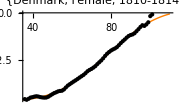

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.109986 | 0.0022125 | 49.711 | 1.14727×10^-51
s | 2.51172 | 0.17658 | 14.2242 | 3.44892×10^-21
a | 8.63354 | 0.178739 | 48.3024 | 6.52385×10^-51
m | 4.77219 | 0.028508 | 167.399 | 4.63683×10^-84

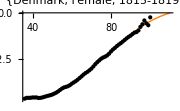

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.107583 | 0.00188524 | 57.0657 | 2.64793×10^-55
s | 2.85039 | 0.208877 | 13.6463 | 2.44523×10^-20
a | 8.46784 | 0.152958 | 55.3606 | 1.67593×10^-54
m | 4.82587 | 0.0261405 | 184.613 | 1.08601×10^-86

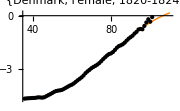

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.116018 | 0.00239446 | 48.4528 | 5.40614×10^-51
s | 2.16996 | 0.138458 | 15.6724 | 3.06703×10^-23
a | 9.14807 | 0.192797 | 47.4493 | 1.91366×10^-50
m | 4.73839 | 0.0268497 | 176.479 | 1.76551×10^-85

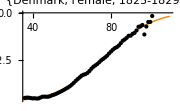

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.119756 | 0.00230972 | 51.8489 | 8.9556×10^-53
s | 2.13098 | 0.126422 | 16.8561 | 7.81889×10^-25
a | 9.47614 | 0.185932 | 50.9655 | 2.53736×10^-52
m | 4.75762 | 0.0247536 | 192.199 | 8.98128×10^-88

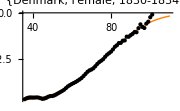

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.123833 | 0.00216949 | 57.0795 | 2.60926×10^-55
s | 1.98011 | 0.102807 | 19.2605 | 7.42152×10^-28
a | 9.81627 | 0.174224 | 56.3428 | 5.75193×10^-55
m | 4.77313 | 0.0221588 | 215.406 | 7.73499×10^-91

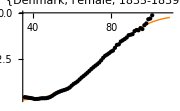

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.127099 | 0.00216096 | 58.8158 | 1.97883×10^-57
s | 1.81358 | 0.0865511 | 20.9539 | 2.35245×10^-30
a | 10.0782 | 0.173306 | 58.1524 | 4.03612×10^-57
m | 4.842 | 0.0224436 | 215.74 | 2.53797×10^-93

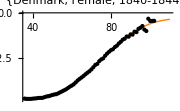

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.13136 | 0.00231567 | 56.7266 | 8.51179×10^-56
s | 1.69158 | 0.0832923 | 20.309 | 2.40253×10^-29
a | 10.408 | 0.184774 | 56.3281 | 1.31596×10^-55
m | 4.83471 | 0.0224627 | 215.233 | 4.87802×10^-92

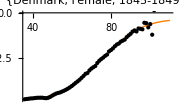

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.131858 | 0.00247765 | 53.2191 | 1.84066×10^-53
s | 1.55258 | 0.0808119 | 19.2123 | 8.48135×10^-28
a | 10.408 | 0.196317 | 53.0165 | 2.32009×10^-53
m | 4.93616 | 0.0255321 | 193.331 | 6.24322×10^-88

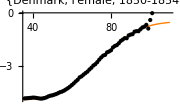

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.121673 | 0.0024318 | 50.0342 | 4.96966×10^-53
s | 1.81631 | 0.101898 | 17.8248 | 1.64988×10^-26
a | 9.57161 | 0.193587 | 49.4434 | 1.04302×10^-52
m | 5.1262 | 0.0342257 | 149.777 | 3.36914×10^-83

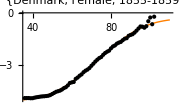

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.115856 | 0.00191552 | 60.4829 | 1.61028×10^-57
s | 1.93195 | 0.0936711 | 20.6248 | 1.02995×10^-29
a | 9.1343 | 0.153035 | 59.6878 | 3.65485×10^-57
m | 5.23149 | 0.0314276 | 166.461 | 5.08656×10^-85

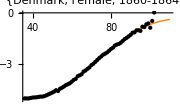

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.109308 | 0.0015568 | 70.2131 | 2.80302×10^-62
s | 2.21832 | 0.102017 | 21.7445 | 2.93055×10^-31
a | 8.64298 | 0.125312 | 68.9714 | 8.65301×10^-62
m | 5.36933 | 0.0316397 | 169.702 | 1.1602×10^-86

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.109276 | 0.00125669 | 86.9556 | 5.49704×10^-69
s | 2.09099 | 0.0735919 | 28.4134 | 2.27951×10^-38
a | 8.68279 | 0.101656 | 85.4131 | 1.74205×10^-68
m | 5.38124 | 0.0256389 | 209.885 | 9.20768×10^-94

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.111973 | 0.00160811 | 69.6301 | 8.84119×10^-63
s | 1.94851 | 0.0832317 | 23.4107 | 2.20414×10^-33
a | 8.97872 | 0.130618 | 68.7404 | 2.01717×10^-62
m | 5.32196 | 0.0288809 | 184.273 | 4.28453×10^-90

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.11143 | 0.0019594 | 56.8694 | 3.71296×10^-57
s | 1.98866 | 0.108322 | 18.3588 | 2.04953×10^-27
a | 9.03007 | 0.160075 | 56.4115 | 6.215×10^-57
m | 5.44456 | 0.0373691 | 145.697 | 1.7648×10^-83

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.10852 | 0.00129331 | 83.9089 | 5.47268×10^-68
s | 2.24933 | 0.0943713 | 23.8349 | 7.73313×10^-34
a | 8.90699 | 0.106746 | 83.4408 | 7.84697×10^-68
m | 5.56462 | 0.0272016 | 204.57 | 4.8666×10^-93

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.107315 | 0.00132782 | 80.8203 | 6.12341×10^-67
s | 2.65243 | 0.145466 | 18.234 | 2.97369×10^-27
a | 8.94636 | 0.110843 | 80.7118 | 6.67638×10^-67
m | 5.6649 | 0.0292959 | 193.368 | 1.88064×10^-91

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.106891 | 0.00116416 | 91.8176 | 1.64629×10^-70
s | 3.06382 | 0.193544 | 15.8301 | 5.49991×10^-24
a | 8.98437 | 0.0975753 | 92.0762 | 1.37314×10^-70
m | 5.86966 | 0.0296457 | 197.994 | 4.05635×10^-92

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.108336 | 0.00103397 | 104.777 | 3.2676×10^-74
s | 3.0597 | 0.175932 | 17.3914 | 3.84608×10^-26
a | 9.1725 | 0.0867747 | 105.705 | 1.848×10^-74
m | 6.02099 | 0.0280101 | 214.958 | 1.95444×10^-94

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0937112 | 0.00217881 | 43.0103 | 8.55234×10^-47
s | 3.61065 | 0.511129 | 7.06406 | 1.94511×10^-9
a | 7.05813 | 0.174757 | 40.3882 | 3.29069×10^-45
m | 4.78527 | 0.0418736 | 114.279 | 6.59012×10^-72

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0927118 | 0.00207577 | 44.6638 | 3.46817×10^-47
s | 4.80972 | 1.62884 | 2.95285 | 0.0045144
a | 7.01039 | 0.166603 | 42.0785 | 1.05238×10^-45
m | 4.88798 | 0.043403 | 112.619 | 1.41688×10^-70

-Graphics-

General::munfl: Exp[-2229.22] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0907153 | 0.000986423 | 91.9638 | 3.85235×10^-67
s | 127.445 | 2.27937×10^-15 | 5.59124×10^16 | 0.
a | 6.88091 | 0.0893945 | 76.9723 | 1.82017×10^-62
m | 4.94322 | 0.0367704 | 134.435 | 3.77518×10^-77

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0893298 | 0.00228175 | 39.1496 | 1.96556×10^-45
s | 6.73129 | 11.5985 | 0.580359 | 0.563776
a | 6.75267 | 0.185466 | 36.4092 | 1.46975×10^-43
m | 5.03284 | 0.0595775 | 84.4756 | 9.91208×10^-66

-Graphics-

General::munfl: Exp[-2277.04] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0929479 | 0.000918911 | 101.15 | 1.20127×10^-69
s | 35.1335 | 2.86904×10^-16 | 1.22457×10^17 | 0.
a | 7.10793 | 0.0831491 | 85.4842 | 3.21112×10^-65
m | 4.97531 | 0.0328533 | 151.44 | 2.69593×10^-80

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0976618 | 0.00166631 | 58.6095 | 5.21252×10^-56
s | 3.29388 | 0.284119 | 11.5933 | 3.62828×10^-17
a | 7.49927 | 0.134768 | 55.6459 | 1.22611×10^-54
m | 4.92482 | 0.0323407 | 152.279 | 1.61831×10^-81

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0966902 | 0.0019052 | 50.7507 | 1.32734×10^-51
s | 4.63851 | 1.2448 | 3.72632 | 0.000427075
a | 7.47926 | 0.154631 | 48.3686 | 2.32363×10^-50
m | 5.04514 | 0.0405011 | 124.568 | 3.88247×10^-75

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0982752 | 0.00233759 | 42.0412 | 9.40975×10^-47
s | 4.04512 | 0.844988 | 4.78719 | 0.0000111603
a | 7.61595 | 0.189709 | 40.1455 | 1.42539×10^-45
m | 5.00948 | 0.0468944 | 106.825 | 4.38126×10^-71

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.108386 | 0.00274367 | 39.504 | 1.14833×10^-45
s | 2.48054 | 0.21555 | 11.508 | 4.9714×10^-17
a | 8.45264 | 0.220849 | 38.2734 | 7.57093×10^-45
m | 4.92303 | 0.0422927 | 116.404 | 2.61627×10^-74

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.111769 | 0.002189 | 51.0593 | 2.26984×10^-52
s | 2.24889 | 0.138272 | 16.2642 | 4.79573×10^-24
a | 8.73658 | 0.175603 | 49.7519 | 1.09163×10^-51
m | 4.95773 | 0.0324173 | 152.935 | 1.24079×10^-81

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.111442 | 0.00215405 | 51.7358 | 1.0224×10^-52
s | 2.16997 | 0.129319 | 16.7799 | 9.85234×10^-25
a | 8.72984 | 0.172647 | 50.5648 | 4.0929×10^-52
m | 5.0513 | 0.0339372 | 148.843 | 6.63767×10^-81

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.103381 | 0.00209419 | 49.3658 | 4.46819×10^-52
s | 2.97987 | 0.273664 | 10.8888 | 4.06655×10^-16
a | 8.11835 | 0.169541 | 47.8843 | 2.90072×10^-51
m | 5.31591 | 0.0471825 | 112.667 | 2.23817×10^-74

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.107129 | 0.00203714 | 52.5881 | 2.21306×10^-54
s | 2.45783 | 0.164846 | 14.9099 | 1.69613×10^-22
a | 8.44318 | 0.164193 | 51.4223 | 8.99278×10^-54
m | 5.40274 | 0.0453076 | 119.246 | 6.9355×10^-77

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.109139 | 0.00225577 | 48.3822 | 4.03517×10^-52
s | 2.31253 | 0.160583 | 14.4009 | 9.47397×10^-22
a | 8.64492 | 0.181883 | 47.5302 | 1.22032×10^-51
m | 5.45594 | 0.0496532 | 109.881 | 1.26918×10^-74

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110548 | 0.00246033 | 44.9324 | 1.13908×10^-50
s | 2.09501 | 0.144318 | 14.5166 | 4.50928×10^-22
a | 8.77046 | 0.198089 | 44.2753 | 2.88028×10^-50
m | 5.556 | 0.0567875 | 97.8384 | 2.7309×10^-72

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.10302 | 0.00142922 | 72.0807 | 9.60268×10^-64
s | 2.52432 | 0.129791 | 19.4492 | 8.51292×10^-29
a | 8.1596 | 0.115447 | 70.6782 | 3.39008×10^-63
m | 5.97674 | 0.0538456 | 110.998 | 7.85063×10^-76

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.103973 | 0.00140437 | 74.0359 | 1.72124×10^-64
s | 2.3085 | 0.105906 | 21.7975 | 1.3622×10^-31
a | 8.23131 | 0.112913 | 72.8999 | 4.64763×10^-64
m | 6.09428 | 0.0565163 | 107.832 | 5.09693×10^-75

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.101353 | 0.00173516 | 58.4112 | 6.74266×10^-58
s | 2.36099 | 0.140242 | 16.8351 | 2.17983×10^-25
a | 7.97199 | 0.138757 | 57.453 | 1.93664×10^-57
m | 6.45929 | 0.102603 | 62.954 | 5.63389×10^-60

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0979972 | 0.00180336 | 54.3416 | 6.71691×10^-56
s | 2.53031 | 0.174003 | 14.5418 | 4.1356×10^-22
a | 7.67547 | 0.144038 | 53.2879 | 2.33325×10^-55
m | 6.95349 | 0.18216 | 38.1725 | 3.11096×10^-46

-Graphics-

General::munfl: Exp[-2229.22] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.126478 | 0.00342255 | 36.9543 | 6.08772×10^-44
s | 1.55144 | 0.105843 | 14.6579 | 8.15609×10^-22
a | 9.8133 | 0.27182 | 36.1022 | 2.42748×10^-43
m | 4.33251 | 0.0265475 | 163.199 | 2.23302×10^-83

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.121231 | 0.00533267 | 22.7337 | 1.77338×10^-31
s | 1.87186 | 0.223445 | 8.37727 | 9.89148×10^-12
a | 9.45971 | 0.425803 | 22.2162 | 6.22461×10^-31
m | 4.36828 | 0.0423591 | 103.125 | 3.71792×10^-70

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.127193 | 0.00457186 | 27.8209 | 1.85258×10^-37
s | 1.6201 | 0.150315 | 10.7781 | 5.07065×10^-16
a | 9.94608 | 0.364217 | 27.3081 | 5.56286×10^-37
m | 4.38458 | 0.034197 | 128.215 | 6.81674×10^-79

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.126143 | 0.00450475 | 28.0022 | 2.92224×10^-37
s | 1.69332 | 0.161804 | 10.4652 | 2.06122×10^-15
a | 9.8907 | 0.358882 | 27.5597 | 7.39763×10^-37
m | 4.46774 | 0.0358142 | 124.748 | 3.76089×10^-77

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.123597 | 0.00405442 | 30.4845 | 1.99174×10^-39
s | 1.80935 | 0.162054 | 11.1651 | 1.42614×10^-16
a | 9.69987 | 0.323869 | 29.95 | 5.65594×10^-39
m | 4.55706 | 0.0359775 | 126.664 | 1.44485×10^-77

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.124323 | 0.00384373 | 32.3444 | 5.95369×10^-41
s | 1.78486 | 0.150573 | 11.8537 | 1.08832×10^-17
a | 9.78135 | 0.307261 | 31.834 | 1.53192×10^-40
m | 4.62606 | 0.0353369 | 130.913 | 1.82168×10^-78

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.119501 | 0.00345897 | 34.5481 | 3.27088×10^-42
s | 2.08238 | 0.181004 | 11.5046 | 5.0331×10^-17
a | 9.42054 | 0.277594 | 33.9364 | 9.37437×10^-42
m | 4.70283 | 0.0357532 | 131.536 | 1.38025×10^-77

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.120802 | 0.00361708 | 33.3977 | 3.2614×10^-42
s | 2.06512 | 0.184759 | 11.1774 | 1.09536×10^-16
a | 9.54275 | 0.290321 | 32.8697 | 8.55735×10^-42
m | 4.80415 | 0.0397384 | 120.894 | 2.89149×10^-77

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.128707 | 0.00343682 | 37.4494 | 1.02251×10^-45
s | 1.61011 | 0.117729 | 13.6764 | 8.47396×10^-21
a | 10.1531 | 0.273265 | 37.1547 | 1.6707×10^-45
m | 4.81173 | 0.0339436 | 141.757 | 1.04286×10^-82

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.125186 | 0.00292065 | 42.8623 | 2.21395×10^-49
s | 1.62717 | 0.103324 | 15.7482 | 7.19349×10^-24
a | 9.83917 | 0.23171 | 42.4634 | 3.98263×10^-49
m | 4.9959 | 0.0352532 | 141.715 | 1.06312×10^-82

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.121352 | 0.00225166 | 53.8947 | 1.13574×10^-55
s | 1.61928 | 0.0817207 | 19.8148 | 3.0137×10^-29
a | 9.55745 | 0.179096 | 53.365 | 2.1283×10^-55
m | 5.11648 | 0.0310777 | 164.635 | 6.40082×10^-87

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110787 | 0.00188535 | 58.7619 | 4.60208×10^-58
s | 2.06624 | 0.105628 | 19.5615 | 6.17816×10^-29
a | 8.7673 | 0.151868 | 57.7297 | 1.42549×10^-57
m | 5.33009 | 0.0361087 | 147.613 | 7.56966×10^-84

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.109694 | 0.0016639 | 65.926 | 2.94041×10^-61
s | 1.99095 | 0.0898724 | 22.1531 | 5.38108×10^-32
a | 8.73084 | 0.134501 | 64.9127 | 7.92921×10^-61
m | 5.37813 | 0.03281 | 163.917 | 8.4972×10^-87

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.109888 | 0.00203496 | 54.0001 | 1.00301×10^-55
s | 2.04313 | 0.1175 | 17.3883 | 3.88301×10^-26
a | 8.84566 | 0.165762 | 53.3635 | 2.13217×10^-55
m | 5.37241 | 0.0383407 | 140.123 | 2.21046×10^-82

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.112293 | 0.00215682 | 52.0641 | 1.02099×10^-54
s | 2.02294 | 0.124629 | 16.2317 | 1.49179×10^-24
a | 9.15625 | 0.176707 | 51.816 | 1.38271×10^-54
m | 5.43677 | 0.0393273 | 138.244 | 5.2999×10^-82

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.10895 | 0.00178694 | 60.9703 | 4.36309×10^-59
s | 2.26445 | 0.133164 | 17.005 | 1.27843×10^-25
a | 8.97361 | 0.147705 | 60.7537 | 5.47708×10^-59
m | 5.66375 | 0.0400697 | 141.347 | 1.2578×10^-82

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.1089 | 0.00183004 | 59.5071 | 2.05884×10^-58
s | 2.57438 | 0.186265 | 13.8211 | 5.08013×10^-21
a | 9.10018 | 0.152671 | 59.6066 | 1.8505×10^-58
m | 5.7983 | 0.0433448 | 133.771 | 4.46158×10^-81

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.110594 | 0.00155936 | 70.9225 | 2.71647×10^-63
s | 2.95046 | 0.229744 | 12.8424 | 1.70415×10^-19
a | 9.35551 | 0.130958 | 71.4388 | 1.70532×10^-63
m | 5.89102 | 0.0369181 | 159.57 | 4.85571×10^-86

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.11556 | 0.00153173 | 75.4439 | 5.12937×10^-65
s | 2.83567 | 0.20354 | 13.9318 | 3.44133×10^-21
a | 9.86331 | 0.128818 | 76.568 | 1.98208×10^-65
m | 5.97719 | 0.0343831 | 173.841 | 1.87817×10^-88

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0998028 | 0.00362887 | 27.5024 | 4.43963×10^-36
s | 2.5071 | 0.273821 | 9.15596 | 4.65114×10^-13
a | 7.50797 | 0.29164 | 25.744 | 1.824×10^-34
m | 4.44001 | 0.0507329 | 87.5172 | 7.74351×10^-66

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.103114 | 0.00266826 | 38.6445 | 4.26198×10^-45
s | 2.43889 | 0.193003 | 12.6365 | 8.30222×10^-19
a | 7.82627 | 0.213433 | 36.6685 | 9.65051×10^-44
m | 4.45946 | 0.0328055 | 135.936 | 1.80681×10^-78

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.098516 | 0.00179444 | 54.9006 | 1.21519×10^-53
s | 2.92447 | 0.210339 | 13.9036 | 1.4254×10^-20
a | 7.47397 | 0.144054 | 51.8833 | 3.55858×10^-52
m | 4.57491 | 0.0260309 | 175.749 | 3.13256×10^-84

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.10143 | 0.00198465 | 51.1072 | 2.14447×10^-52
s | 2.58327 | 0.167217 | 15.4487 | 6.25386×10^-23
a | 7.7086 | 0.15884 | 48.5307 | 4.90627×10^-51
m | 4.64006 | 0.0290029 | 159.986 | 7.63796×10^-83

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0987439 | 0.00179133 | 55.1232 | 2.17614×10^-54
s | 3.13004 | 0.255449 | 12.2531 | 3.27555×10^-18
a | 7.54963 | 0.144482 | 52.2529 | 5.59405×10^-53
m | 4.72947 | 0.0291906 | 162.02 | 3.49591×10^-83

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.104558 | 0.00197642 | 52.9028 | 6.32107×10^-54
s | 2.44913 | 0.147771 | 16.5738 | 1.18793×10^-24
a | 8.00883 | 0.15816 | 50.6374 | 9.35674×10^-53
m | 4.7844 | 0.0304738 | 157. | 2.01218×10^-83

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.100721 | 0.00200151 | 50.3226 | 2.19886×10^-51
s | 3.05867 | 0.273041 | 11.2023 | 1.93982×10^-16
a | 7.75155 | 0.161079 | 48.1227 | 3.14621×10^-50
m | 4.86509 | 0.0342421 | 142.079 | 1.30736×10^-78

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.106769 | 0.00208579 | 51.1886 | 4.80676×10^-53
s | 2.562 | 0.174427 | 14.6881 | 5.12437×10^-22
a | 8.27695 | 0.167584 | 49.3899 | 4.33634×10^-52
m | 4.84556 | 0.0313145 | 154.738 | 5.00857×10^-83

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.108142 | 0.00225578 | 47.9401 | 2.70057×10^-51
s | 2.5888 | 0.193872 | 13.3532 | 4.92203×10^-20
a | 8.40271 | 0.180998 | 46.4243 | 1.93523×10^-50
m | 4.9441 | 0.0357771 | 138.192 | 6.09575×10^-80

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.113714 | 0.00246071 | 46.2117 | 7.02509×10^-51
s | 2.13117 | 0.136726 | 15.5872 | 1.80867×10^-23
a | 8.84097 | 0.196223 | 45.0557 | 3.38914×10^-50
m | 5.01995 | 0.0380147 | 132.053 | 1.03967×10^-79

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.112635 | 0.00256833 | 43.8553 | 5.2475×10^-50
s | 2.02977 | 0.133232 | 15.2348 | 3.94455×10^-23
a | 8.76256 | 0.20452 | 42.8444 | 2.27268×10^-49
m | 5.20192 | 0.046226 | 112.532 | 3.23038×10^-76

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.108677 | 0.00241068 | 45.0815 | 9.24413×10^-51
s | 2.18496 | 0.147999 | 14.7633 | 1.93811×10^-22
a | 8.4819 | 0.192728 | 44.0097 | 4.20637×10^-50
m | 5.42301 | 0.0546181 | 99.2896 | 1.05529×10^-72

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.105749 | 0.00217461 | 48.6289 | 7.733×10^-53
s | 2.2412 | 0.146298 | 15.3195 | 2.97282×10^-23
a | 8.29191 | 0.17444 | 47.5346 | 3.2623×10^-52
m | 5.609 | 0.0589659 | 95.1227 | 1.68071×10^-71

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.105343 | 0.0025267 | 41.6917 | 1.25838×10^-48
s | 2.33454 | 0.18895 | 12.3553 | 1.02412×10^-18
a | 8.33633 | 0.203847 | 40.895 | 4.21479×10^-48
m | 5.6557 | 0.0691979 | 81.7323 | 2.97362×10^-67

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.106901 | 0.00301653 | 35.4384 | 3.13396×10^-44
s | 2.20642 | 0.205716 | 10.7255 | 5.10375×10^-16
a | 8.49687 | 0.242822 | 34.9922 | 6.85799×10^-44
m | 5.79135 | 0.0876409 | 66.0805 | 2.53089×10^-61

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.10065 | 0.00215113 | 46.7896 | 8.85131×10^-52
s | 2.62014 | 0.220889 | 11.8618 | 6.49848×10^-18
a | 7.99872 | 0.17418 | 45.9222 | 2.88357×10^-51
m | 6.24726 | 0.105567 | 59.1781 | 2.93302×10^-58

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0994766 | 0.00237674 | 41.8542 | 9.86075×10^-49
s | 2.63248 | 0.248601 | 10.5892 | 8.70128×10^-16
a | 7.88194 | 0.192058 | 41.0393 | 3.38034×10^-48
m | 6.40974 | 0.138839 | 46.1666 | 2.06308×10^-51

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0974004 | 0.0029275 | 33.2708 | 1.5346×10^-42
s | 2.83 | 0.365836 | 7.73571 | 8.60527×10^-11
a | 7.68134 | 0.236629 | 32.4615 | 6.95421×10^-42
m | 6.51115 | 0.199938 | 32.5659 | 5.71242×10^-42

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.105571 | 0.00352272 | 29.9686 | 9.09233×10^-40
s | 2.17126 | 0.233618 | 9.29407 | 1.50792×10^-13
a | 8.32942 | 0.281458 | 29.5938 | 1.94996×10^-39
m | 6.11741 | 0.139663 | 43.8013 | 5.66985×10^-50

-Graphics-

-Graphics-

```mathematica
allNlms=
Table[(
cMxTable=cMxTables[[i]];
cExposureTable=cExposureTables[[i]];
years=Union@cMxTable[[;;,colNames[["Year"]]]];
ages = Union@cMxTable[[;;,colNames[["Age"]]]];
yearRange=Select[years,(binYears@#)[[1]]>countryYearRanges[[i,2]]&&(binYears@#)[[2]]<countryYearRanges[[i,3]]&&(#[[2]]-#[[1]]&@binYears@#==4)&];
nlms=Association@Table[gender->
	Association@Table[y->(
	(*Print[{countriesList[[i]],gender,cohort}];*)
	cMx=Select[cMxTable,First@#==y&&#[[2]]!="110+"&&#[[2]]!=0&][[;;,{"Age",gender}/.colNames]];
	cExposure=Select[cExposureTable,First@#==y&&#[[2]]!="110+"&&#[[2]]!=0&][[;;,{"Age",gender}/.colNames]];
	cDeaths=Select[Transpose@{cExposure[[;;,1]],Log@cMx[[;;,2]],cExposure[[;;,2]]*cMx[[;;,2]]},First@#>35.&];
	data=Select[cDeaths,#[[3]]>4.&&#[[1]]<105.&][[;;,{1,2}]];
	nlm=NonlinearModelFit[data,
	Log [ⅇ^-m+(b ⅇ^s ⅇ^(b x))/(ⅇ^(a+s)-1+ⅇ^(b x))],{{b,0.1},{s,2.8},{a,8.5},{m,6}},x,
	Weights->Sqrt@Select[cDeaths,#[[3]]>4.&&#[[1]]<105.&][[;;,3]]];
	Print[nlm["ParameterTable"]];
	Print[Plot[nlm[x],{x,35,110},Epilog:>Point[data],PlotStyle->{Orange,Thick},ImageSize->Small,PlotLabel->ToString[{countriesList[[i]],gender,y}]]];
	nlm
),{y,yearRange}
],{gender,{"Female","Male"}}
];
Print@GraphicsGrid@Table[Table[
ListPlot[{ToExpression[StringSplit[#,"-"][[1]]],Around[nlms[g][#]["ParameterTableEntries"][[parI,1]],nlms[g][#]["ParameterTableEntries"][[parI,2]]]}&/@yearRange
,AxesLabel->{b,s,a,m}[[parI]]
,PlotLabel->ToString@{countriesList[[i]],g}
,PlotRange->ggmParRanges[[parI]]
],{parI,4}],{g,{"Female","Male"}}];
nlms
),{i,Length@countriesList}];
```

```mathematica
Export["GGM parameters 5 countries.nb",Flatten[Table[Table[Table[{countriesList[[i]],cohort,g,allNlms[[i]][g][cohort]["ParameterTableEntries"][[;;,1;;2]],allNlms[[i]][g][cohort]["CovarianceMatrix"]},{cohort,Keys@allNlms[[i]][g]}],{g,{"Female","Male"}}],{i,Length@allNlms}],2]]
```

General::munfl: Exp[-2229.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2277.04] is too small to represent as a normalized machine number; precision may be lost.

GGM parameters 5 countries.nb

```mathematica
Export["Extrinsic mortality 5 countries.csv",Flatten[Table[Table[Table[{countriesList[[i]],cohort,g,allNlms[[i]][g][cohort]["ParameterTableEntries"][[4,1]]},{cohort,Keys@allNlms[[i]][g]}],{g,{"Female","Male"}}],{i,Length@allNlms}],2]]
```

General::munfl: Exp[-2229.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2277.04] is too small to represent as a normalized machine number; precision may be lost.

Extrinsic mortality 5 countries.csv

```mathematica
Rsquares=Table[
Table[
Table[
allNlms[[i,gender,y]]["AdjustedRSquared"]
,{y,Keys@allNlms[[i,gender]]}]
,{gender,{"Male","Female"}}]
,{i,Length@allNlms}];
```

```mathematica
Fstats=Table[
Table[
Table[
#[[1]]/#[[2]]&@allNlms[[i,gender,y]]["ANOVATableMeanSquares"]
,{y,Keys@allNlms[[i,gender]]}]
,{gender,{"Male","Female"}}]
,{i,Length@allNlms}];
```

```mathematica
{Min@Rsquares,Mean@Mean@Mean@Rsquares}
```

{0.998278,0.999713}

```mathematica
ggmParRanges={{.08,.135},{1.3,4.3},{6.,10.5},{3.5,7.}};
gs=Table[Table[ListLinePlot[
Table[Legended[{ToExpression[StringSplit[#,"-"][[1]]],Around[allNlms[[i,g,#]]["ParameterTableEntries"][[parI,1]],allNlms[[i,g,#]]["ParameterTableEntries"][[parI,2]]]}&/@Keys@allNlms[[i,g]]
,ToString@countriesList[[i]]],{i,{1,2,3,5}}]
,AxesLabel->{b,s,a,m}[[parI]]
,AxesStyle->Directive[Black, Thickness[0.005]]
,PlotLabel->ToString@g
,PlotStyle->Thickness[0.005]
,PlotRange->ggmParRanges[[parI]]
],{g,{"Female","Male"}}],{parI,{4,1,3,2}}];
GraphicsGrid[gs ᵀ]
```

-Graphics-

```mathematica
funcsToPlot={{ⅇ^-m,b,b ⅇ^-a,(*(b ⅇ^s ⅇ^(b *40))/(ⅇ^(a+s)-1+ⅇ^(b *40)),*)ⅇ^-m+b ⅇ^s},{"Extrinsic hazard","Gompertz slope","Gompertz intercept",(*"Aging hazard at 40",*) "Asymptotic hazard"},{"Log10",None,"Log10",(*"Log10",*)"Log10"},{{0.002,0.02},{0.08,0.135},{0.000004,0.0002},(*{0.0005,0.008},*){0.5,5.}}}ᵀ;
gs2=Table[Table[ListLinePlot[
Table[Legended[{
ToExpression[StringSplit[#,"-"][[1]]],
funcInfo[[1]]/.(#[[1]]->#[[2]]&/@({{b,s,a,m},(Around[#[[1]],#[[2]]]&)/@allNlms[[i,g,#]]["ParameterTableEntries"]}ᵀ))
}&/@Keys@allNlms[[i,g]]
,ToString@countriesList[[i]]],{i,{1,2,3,5}}]
,AxesLabel->funcInfo[[2]]
,ScalingFunctions->funcInfo[[3]]
,AxesStyle->Directive[Black, Thickness[0.007]]
,PlotLabel->ToString@g
,PlotStyle->Thickness[0.005]
,PlotRange->{Automatic,funcInfo[[4]]}
],{g,{"Female","Male"}}],{funcInfo,funcsToPlot}];
GraphicsGrid[gs2]
```

-Graphics-

```mathematica
GraphicsGrid[gs2ᵀ]
```

-Graphics-

```mathematica
Basedir="/Users/yifan/Library/CloudStorage/Dropbox/Current Projects/2023-AlonbLab-sickspans/Human healthspan/";
imported=NotebookImport[Basedir<>"Human GG-SR mapping powerlaws.nb",_->"Expression"][[1]];
SRparNames=imported[[1]];
GGpars=imported[[2]];
GGSRpowerlaws=imported[[3]];
imported=NotebookImport[Basedir<>"Human GG-SR mapping powerlaws originGGpars.nb",_->"Expression"][[1]];
karinGGpar=imported[[1,1]];
micePar={Around[ 0.084/365,.25*10^-4],Around[.15,.022],Around[.5,.1], Around[.16,.02],Around[17,2.5]};
karinSRpar=Prepend[Rest@micePar,First@micePar/60.][[{1,2,4,5}]];
```

```mathematica
correlatedNormSum[mu_, cov_, ws_]:=(
n=Length@mu;
std=Sqrt[Dot[mu^2,ws^2]+2*Total@Flatten@Table[Table[ws[[i]]*ws[[j]]*cov[[i,j]],{j,Range[i+1,n]}],{i,n-1}]];
Around[Dot[mu,ws],std]
);
vectorAroundLog[mu_,cov_]:=(
n=Length@mu;
varLog=Table[Table[Mean[{cov[[i,j]]/(mu[[i]]*mu[[j]]),cov[[j,i]]/(mu[[j]]*mu[[i]])}],{j,n}],{i,n}];
VectorAround[Log@mu,varLog]
)
```

```mathematica
varsMatrix={{1,0,0},{0,1,0},{0,1,0},{0,0,1}};
varNames=Exp@Dot[Log@SRparNames,varsMatrix];
A=Dot[Transpose@GGSRpowerlaws[[;;,;;,2]],varsMatrix];
```

```mathematica
MatrixForm[{{1,0,0},{0,1,0},{0,1,0},{0,0,1}}ᵀ]
```

(1 | 0 | 0 | 0
0 | 1 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
varsMatrix={{0,0,0},{1,0,0},{0,1,0},{0,0,1}};
varNames=Exp@Dot[Log@SRparNames,varsMatrix];
A=Dot[Transpose@GGSRpowerlaws[[;;,;;,2]],varsMatrix];
```

```mathematica
Needs["CCompilerDriver`"]
sf=Compile[{{η,_Real},{β,_Real},{k,_Real},{ϵ,_Real},{Xc,_Real},{n,_Integer}},
Table[
Block[{X,i},X=0.0;i=0;
While[Xc>(X=# UnitStep[#]&@( (++i)η +UnitStep[X](X-β X/(k+X)+√(2 ϵ)RandomReal[NormalDistribution[0,1.]])))];
N@i],
n],
CompilationTarget->"C",Parallelization->True,RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
eventTimes2HazardData[eventTimes_]:=(
lifespans=Sort@eventTimes/365.;
maxAge=Floor@Max@lifespans;
startAge=Floor@lifespans[[Round[Length@lifespans*.25]]];
exposures = Table[
Total[Select[lifespans,#>t&&#<=t+1&]-t]+
Length@Select[lifespans,#>t+1&]
,{t,startAge,maxAge}];
deaths= BinCounts[lifespans,{startAge,maxAge+1,1}];
data={#[[1]],Log[#[[2]]/#[[3]]],#[[3]]}&/@Select[Transpose@{Range[startAge,maxAge],deaths,exposures},#[[2]]>0&&#[[3]]>4&]
);
GGfitData[eventTimes_, b0_:.095,s0_:2.255,a0_:9.6]:=(
data=eventTimes2HazardData[eventTimes];
nlm=NonlinearModelFit[data[[;;,1;;2]],
Log@((b ⅇ^s ⅇ^(b x))/(ⅇ^a-1+ⅇ^(b x))),{{b,b0},{s,s0},{a,a0}},x,
Weights->Sqrt@data[[;;,3]]];
{nlm,data}
);
```

```mathematica
i=1;
g="Female";
cohortRange=Keys@allNlms[[i]][g];
refGGpar=VectorAround[#["ParameterTableEntries"][[;;,1]][[;;3]],  N[(#+#ᵀ)/2]&@#["CovarianceMatrix"][[;;3,;;3]]]&@allNlms[[i]][g]["1890-1894"];
estimatedCohortParFCs=Table[(
cohortGGpar=VectorAround[#["ParameterTableEntries"][[;;,1]][[;;3]],  N[(#+#ᵀ)/2]&@#["CovarianceMatrix"][[;;3,;;3]]]&@allNlms[[i]][g][cohort];
deltaGGpar=vectorAroundLog@@cohortGGpar[[1;;2]]-vectorAroundLog@@refGGpar[[1;;2]];
(*sol=Dot[Inverse@A,deltaGGpar];*)
sol=Table[correlatedNormSum[deltaGGpar[[1]], deltaGGpar[[2]],Inverse[A][[i]]],{i,3}];
#[[1]]->#[[2]]&/@Transpose@{varNames,sol}
),{cohort,cohortRange}];
GraphicsGrid@Table[{
ListLinePlot[Table[
{
ToExpression[StringSplit[cohortRange[[j]],"-"][[1]]],
par/.estimatedCohortParFCs[[j]]
},
{j,Length@cohortRange}],
AxesLabel->(*"Log("<>ToString@par<>")"*)par,
PlotRange->Automatic
]},{par,varNames}]
```

-Graphics-

```mathematica
Nsample=5*10^4;
originEventTimes=sf[##,Nsample]&@@Insert[karinSRpar[[;;,1]],.5,3];
originFit=GGfitData[originEventTimes];
```

```mathematica
Exp[-m]/.allNlms[[1,"Female",#]]["BestFitParameters"]&/@{"1890-1894","1820-1824"}
```

{0.00362748,0.00830689}

```mathematica
perturbedSRpar=Insert[(karinSRpar[[;;,1]]*{η,β,ϵ,Xc}/.{η->Exp@.995,β->Exp@1.1,Xc->Exp@0.16,ϵ->Exp@1.1}),.5,3];
perturbedEventTimes=sf[##,Nsample]&@@perturbedSRpar;
perturbedFit=GGfitData[perturbedEventTimes];
```

```mathematica
{#[[1]],Exp@#[[2]]}&/@allhazards[[1,"Female","1890-1894"]]
```

{{36,0.004434},{37,0.004275},{38,0.00456},{39,0.004334},{40,0.004267},{41,0.004462},{42,0.004882},{43,0.00465},{44,0.004728},{45,0.005223},{46,0.005087},{47,0.005271},{48,0.005701},{49,0.005578},{50,0.005822},{51,0.006367},{52,0.006613},{53,0.007012},{54,0.007414},{55,0.007795},{56,0.008667},{57,0.009222},{58,0.009822},{59,0.010438},{60,0.011331},{61,0.012185},{62,0.01257},{63,0.014529},{64,0.015463},{65,0.016815},{66,0.018556},{67,0.020855},{68,0.022407},{69,0.024625},{70,0.028033},{71,0.030504},{72,0.033662},{73,0.037492},{74,0.042187},{75,0.047393},{76,0.051428},{77,0.057162},{78,0.062663},{79,0.068025},{80,0.074023},{81,0.083221},{82,0.092738},{83,0.101282},{84,0.11122},{85,0.124792},{86,0.134407},{87,0.14869},{88,0.16223},{89,0.179584},{90,0.196678},{91,0.215614},{92,0.232503},{93,0.255111},{94,0.272871},{95,0.306923},{96,0.34725},{97,0.352985},{98,0.398449},{99,0.438349},{100,0.480069},{101,0.504979},{102,0.48},{103,0.554822},{104,0.65625}}

```mathematica
g01=Plot[{originFit[[1]][x],allNlms[[1,"Female","1890-1894"]][x]},{x,60,106},PlotStyle->{Automatic,Dashed}
(*,PlotLegends->{
"Karin parameters "<>ToString@{η,β,κ,ϵ,Xc},
"Swedish women born 1890-1894"}*)
,Epilog:>Point[allhazards[[i]]["Female"]["1890-1894"]]
];
g02=Plot[Evaluate[#[x]&/@#1],{x,60,106},PlotStyle->#2(*,PlotLegends->#3*)]&@@{
{originFit[[1]],perturbedFit[[1]]},
{Automatic,Dashed},
{"Karin parameters "<>ToString@{η,β,κ,ϵ,Xc},
"Reference parameter "<>ToString@{η0,β0,κ0,ϵ0,Xc0}}
};
g03=Plot[Exp@Evaluate[perturbedFit[[1]][x]]+Exp[-m]/.allNlms[[1,"Female","1890-1894"]]["BestFitParameters"],{x,35,106}
,PlotStyle->Orange
(*,PlotLegends->"SR model + extrinsic hazard"*)
,ScalingFunctions->"Log10"
,Epilog->{PointSize[0.008] ,Point[{#[[1]],Log10@Exp@#[[2]]}&/@allhazards[[1,"Female","1890-1894"]]]}
];
GraphicsGrid[{Show[#,AxesStyle->Directive[Black, Thickness@0.005]]}&/@{g01,g02,g03}]
```

-Graphics-

```mathematica
data=#[[2]]&/@allhazards[[1,"Female","1890-1894"]];
model=Log[Exp@perturbedFit[[1]]["BestFit"]/.{x->First@#}&/@allhazards[[1,"Female","1890-1894"]]+Exp[-m]/.allNlms[[1,"Female","1890-1894"]]["BestFitParameters"]];
weights=allweights[[1,"Female","1890-1894"]];
SSentries=Dot[weights,#^2&/@#]&/@{model,data-model,data,data-Mean@data,model-Mean@data};
MSentries={SSentries[[4]]/(Length@data-1),SSentries[[2]]/(Length@data-1-4)};
{1-#[[2]]/#[[4]]&@SSentries,1-#[[2]]/#[[1]]&@MSentries,#[[5]]/#[[2]]&@SSentries}
```

{0.999478,0.999445,1878.63}

```mathematica
period1SRpar=perturbedSRpar*Insert[{η,β,ϵ,Xc}/.{η->Exp@.13,β->Exp@.1,Xc->Exp@-.01,ϵ->Exp@.1},1.,3];
period1EventTimes=sf[##,Nsample]&@@period1SRpar;
period1Fit=GGfitData[period1EventTimes];
```

```mathematica
g12=Plot[Evaluate[#[x]&/@#1],{x,75,105},PlotStyle->#2(*,PlotLegends->#3*)]&@@{
{perturbedFit[[1]],period1Fit[[1]]},
{Automatic,Dashed},
{ToString@{η0,β0,κ0,ϵ0,Xc0},StringRiffle[#1->ToString[NumberForm[#2,3]]<>"*"<>ToString@#3&@@@Transpose@{{η,β,κ,ϵ,Xc},period1SRpar/perturbedSRpar,{η0,β0,κ0,ϵ0,Xc0}},"\n"]}
};
g11=Plot[Evaluate[allNlms[[1,"Female",#]][x]&/@#1],{x,75,105},PlotStyle->#2,(*PlotLegends->#1,*)Epilog:>{
{Blue,Point[allhazards[[1,"Female",#1[[1]]]]]},
{Orange,Point[allhazards[[1,"Female",#1[[2]]]]]}
}]&@@{{"1890-1894","1820-1824"},{ColorData[97,"ColorList"][[1]],Directive[Dashed,ColorData[97,"ColorList"][[2]]]}};
g13=Plot[Exp@Evaluate[period1Fit[[1]][x]]+Exp[-m]/.allNlms[[1,"Female","1820-1824"]]["BestFitParameters"],{x,35,106}
,PlotStyle->Orange
,ScalingFunctions->"Log10"
,Epilog:>{PointSize[0.008] ,Point[{#[[1]],Log10@Exp@#[[2]]}&/@allhazards[[1,"Female","1820-1824"]]]}
];
GraphicsGrid[{Show[#,AxesStyle->Directive[Black, Thickness@0.005]]}&/@{g11,g12,g13}]
```

-Graphics-

```mathematica
data=#[[2]]&/@allhazards[[1,"Female","1820-1824"]];
model=Log[Exp@period1Fit[[1]]["BestFit"]/.{x->First@#}&/@allhazards[[1,"Female","1820-1824"]]+Exp[-m]/.allNlms[[1,"Female","1820-1824"]]["BestFitParameters"]];
weights=allweights[[1,"Female","1820-1824"]];
SSentries=Dot[weights,#^2&/@#]&/@{model,data-model,data,data-Mean@data,model-Mean@data};
MSentries={SSentries[[4]]/(Length@data-1),SSentries[[2]]/(Length@data-1-4)};
{1-#[[2]]/#[[4]]&@SSentries,1-#[[2]]/#[[1]]&@MSentries,#[[5]]/#[[2]]&@SSentries}
```

{0.998748,0.998669,782.286}

```mathematica
GraphicsGrid[{Show[#
,AxesStyle->Directive[Black, Thickness@0.002]
,PlotStyle->Thickness@0.001
,PlotRange->{{35,105},{-2.5,0}}
]}&/@{g13,g03}]
```

-Graphics-

```mathematica
Plot[
{Exp@Evaluate[period1Fit[[1]][x]]+Exp[-m]/.allNlms[[1,"Female","1820-1824"]]["BestFitParameters"],
Exp@Evaluate[perturbedFit[[1]][x]]+Exp[-m]/.allNlms[[1,"Female","1890-1894"]]["BestFitParameters"]
},{x,35,106}
,PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]}
,PlotLegends->{"Born 1820-1824","Born 1890-1894"}
,ScalingFunctions->"Log10"
,Epilog:>{
{PointSize[0.008] ,Point[{#[[1]],Log10@Exp@#[[2]]}&/@allhazards[[1,"Female","1820-1824"]]]},
{PointSize[0.008] ,Point[{#[[1]],Log10@Exp@#[[2]]}&/@allhazards[[1,"Female","1890-1894"]]]}
}
,AxesStyle->Directive[Black, Thickness@0.002]
,PlotStyle->Thickness@0.001
,PlotRange->{{35,105},Automatic}
]
```

-Graphics-

```mathematica
Plot[
{Exp@Evaluate[perturbedFit[[1]][x]],
Exp@Evaluate[perturbedFit[[1]][x]]+Exp[-m]/.allNlms[[1,"Female","1890-1894"]]["BestFitParameters"],
},{x,35,106}
,PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]}
,PlotLegends->{"SR model","SR model +"<>"\n"<>"exstrinsic hazard"}
,ScalingFunctions->"Log10"
,Epilog:>{
{PointSize[0.008] ,Point[{#[[1]],Log10@Exp@#[[2]]}&/@allhazards[[1,"Female","1890-1894"]]]}
}
,AxesStyle->Directive[Black, Thickness@0.002]
,PlotStyle->Thickness@0.001
,PlotRange->{{35,105},Full}
]
```

-Graphics-

```mathematica
period3SRpar=perturbedSRpar*Insert[{η,β,ϵ,Xc}/.{η->Exp@1.76,β->Exp@1.958,Xc->Exp@.12,ϵ->Exp@1.958},1.,3];
period3EventTimes=sf[##,Nsample]&@@period3SRpar;
period3Fit=GGfitData[period3EventTimes];
period2Fit=perturbedFit;
```

```mathematica
g22=Plot[Evaluate[#[x]&/@#1],{x,65,105},PlotStyle->#2,PlotLegends->#3]&@@{
{period2Fit[[1]],period3Fit[[1]]},
{Automatic,Dashed},
{ToString@{η0,β0,κ0,ϵ0,Xc0},StringRiffle[#1->ToString[NumberForm[#2,3]]<>"*"<>ToString@#3&@@@Transpose@{{η,β,κ,ϵ,Xc},period3SRpar/perturbedSRpar,{η0,β0,κ0,ϵ0,Xc0}},"\n"]}
}
```

-Graphics-

```mathematica
g21=Plot[Evaluate[allNlms[[1]]["Female"][#][x]&/@#1],{x,65,105},PlotStyle->#2,PlotLegends->#1,Epilog:>{
{Blue,Point[allhazards[[1]]["Female"][#1[[1]]]]},
{Orange,Point[allhazards[[1]]["Female"][#1[[2]]]]}
}]&@@{{"1880-1884","1905-1909"},{ColorData[97,"ColorList"][[1]],Directive[Dashed,ColorData[97,"ColorList"][[2]]]}}
```

-Graphics-

```mathematica
period1SRpar=perturbedSRpar*Insert[{η,β,ϵ,Xc}/.{η->Exp@.182,β->Exp@.182,Xc->Exp@0.,ϵ->Exp@.182},1.,3];
period1EventTimes=sf[##,Nsample]&@@period1SRpar;
period1Fit=GGfitData[period1EventTimes];
```

```mathematica
g12=Plot[Evaluate[#[x]&/@#1],{x,70,105},PlotStyle->#2,PlotLegends->#3]&@@{
{period2Fit[[1]],period1Fit[[1]]},
{Automatic,Dashed},
{ToString@{η0,β0,κ0,ϵ0,Xc0},StringRiffle[#1->ToString[NumberForm[#2,3]]<>"*"<>ToString@#3&@@@Transpose@{{η,β,κ,ϵ,Xc},period1SRpar/perturbedSRpar,{η0,β0,κ0,ϵ0,Xc0}},"\n"]}
}
```

-Graphics-

```mathematica
g21=Plot[Evaluate[allNlms[[1]]["Female"][#][x]&/@#1],{x,70,105},PlotStyle->#2,PlotLegends->#1,Epilog:>{
{Blue,Point[allhazards[[1]]["Female"][#1[[1]]]]},
{Orange,Point[allhazards[[1]]["Female"][#1[[2]]]]}
}]&@@{{"1880-1884","1865-1869"},{ColorData[97,"ColorList"][[1]],Directive[Dashed,ColorData[97,"ColorList"][[2]]]}}
```

-Graphics-

```mathematica
i=2;
g="Male";
cohortRange=Keys@allNlms[[i]][g];
refGGpar=VectorAround[#["ParameterTableEntries"][[;;,1]][[;;3]],  N[(#+#ᵀ)/2]&@#["CovarianceMatrix"][[;;3,;;3]]]&@allNlms[[i]][g]["1885-1889"];
estimatedCohortParFCs=Table[(
cohortGGpar=VectorAround[#["ParameterTableEntries"][[;;,1]][[;;3]],  N[(#+#ᵀ)/2]&@#["CovarianceMatrix"][[;;3,;;3]]]&@allNlms[[i]][g][cohort];
deltaGGpar=vectorAroundLog@@cohortGGpar[[1;;2]]-vectorAroundLog@@refGGpar[[1;;2]];
(*sol=Dot[Inverse@A,deltaGGpar];*)
sol=Table[correlatedNormSum[deltaGGpar[[1]], deltaGGpar[[2]],Inverse[A][[i]]],{i,3}];
#[[1]]->#[[2]]&/@Transpose@{varNames,sol}
),{cohort,cohortRange}];
GraphicsGrid@Table[{
ListLinePlot[Table[
{
ToExpression[StringSplit[cohortRange[[j]],"-"][[1]]],
par/.estimatedCohortParFCs[[j]]
},
{j,Length@cohortRange}],
AxesLabel->(*"Log("<>ToString@par<>")"*)par,
PlotRange->Automatic
]},{par,varNames}]
```

-Graphics-

```mathematica
perturbedMSRpar=Insert[(karinSRpar[[;;,1]]*{η,β,ϵ,Xc}/.{η->Exp@.26,β->Exp@.315,Xc->Exp@-.04,ϵ->Exp@.315}),.5,3];
perturbedMEventTimes=sf[##,Nsample]&@@perturbedMSRpar;
perturbedMFit=GGfitData[perturbedMEventTimes];
```

```mathematica
f02=Plot[Evaluate[#[x]&/@#1],{x,70,105},PlotStyle->#2,PlotLegends->#3]&@@{
{originFit[[1]],perturbedMFit[[1]]},
{Automatic,Dashed},
{"Karin parameters "<>ToString@{η,β,κ,ϵ,Xc},
"Reference parameter "<>ToString@{η0,β0,κ0,ϵ0,Xc0}}
}
```

-Graphics-

```mathematica
f01=Plot[{originFit[[1]][x],allNlms[[i]]["Male"]["1885-1889"][x]},{x,70,105},PlotStyle->{Automatic,Dashed}
,PlotLegends->{
"Karin parameters "<>ToString@{η,β,κ,ϵ,Xc},
"English men born 1885-1889"}
,Epilog:>Point[allhazards[[i]]["Male"]["1885-1889"]]
]
```

-Graphics-

```mathematica
estimatedCohortParFCs[[3]]
```

{η→0.70.6,β ε→0.80.7,Xc→0.0390.025}

```mathematica
period1MSRpar=perturbedMSRpar*Insert[{η,β,ϵ,Xc}/.{η->Exp@.4,β->Exp@.45,Xc->Exp@-.01,ϵ->Exp@.45},1.,3];
period1MEventTimes=sf[##,Nsample]&@@period1MSRpar;
period1MFit=GGfitData[period1MEventTimes];
```

```mathematica
f12=Plot[Evaluate[#[x]&/@#1],{x,70,105},PlotStyle->#2,PlotLegends->#3]&@@{
{period1MFit[[1]],perturbedMFit[[1]]},
{Automatic,Dashed},
{ToString@{η0,β0,κ0,ϵ0,Xc0},StringRiffle[#1->ToString[NumberForm[#2,3]]<>"*"<>ToString@#3&@@@Transpose@{{η,β,κ,ϵ,Xc},period1MSRpar/perturbedMSRpar,{η0,β0,κ0,ϵ0,Xc0}},"\n"]}
}
```

-Graphics-

```mathematica
f11=Plot[Evaluate[allNlms[[2]]["Male"][#][x]&/@#1],{x,70,105},PlotStyle->#2,PlotLegends->#1,Epilog:>{
{Blue,Point[allhazards[[2]]["Male"][#1[[1]]]]},
{Orange,Point[allhazards[[2]]["Male"][#1[[2]]]]}
}]&@@{{"1850-1854","1885-1889"},{ColorData[97,"ColorList"][[1]],Directive[Dashed,ColorData[97,"ColorList"][[2]]]}}
```

-Graphics-